## Variables, Decay Rates

### Relations for α angle and physical masses

#### Relations for the α angle Eq. 2.7 of Curtin, 2015.

```mathematica
δ2[ϵ_,mzd0_]:= mzd0^2/(mz0^2(1-ϵ^2/Cosw^2))
```

```mathematica
η[ϵ_] := ϵ/(Cosw √(1-ϵ^2/Cosw^2));
```

```mathematica
Tanα[ϵ_,mzd0_] := (1-η[ϵ]^2 Sinw^2-δ2[ϵ,mzd0]-Sign[1-δ2[ϵ,mzd0]] √(4 η[ϵ]^2 Sinw^2+(1-η[ϵ]^2 Sinw^2-δ2[ϵ,mzd0])^2))/(2 η[ϵ] Sinw);
```

```mathematica
Sinα[ϵ_,mzd0_] := Tanα[ϵ,mzd0]/(√(1 +Tanα[ϵ,mzd0]^2))
Cosα[ϵ_,mzd0_] := 1/(√(1 +Tanα[ϵ,mzd0]^2))
```

#### Relations for the physical masses m_z and m_ZD (2.8 of Curtin)

```mathematica
massaZ[ϵ_,mzd0_]:=Sqrt[mz0^2/2(1+δ2[ϵ,mzd0]+η[ϵ]^2 Sinw^2+Sign[1-δ2[ϵ,mzd0]] √((1+δ2[ϵ,mzd0]+η[ϵ]^2 Sinw^2)^2-4  δ2[ϵ,mzd0]))]
```

```mathematica
massaZD[ϵ_,mzd0_]:=Sqrt[mz0^2/2(1+δ2[ϵ,mzd0]+η[ϵ]^2 Sinw^2-Sign[1-δ2[ϵ,mzd0]] √((1+δ2[ϵ,mzd0]+η[ϵ]^2 Sinw^2)^2-4  δ2[ϵ,mzd0]))]
```

### Z boson decay width (Zboson-decaywidth.nb, and Fermionic_Thermal_Average_Relatorio_Parcial.nb)

```mathematica
Γztotaldk[ϵ_,mx_,gD_]:= HeavisideTheta[mz-2mx]((-gD^2 √(1-(4 mx^2)/mz^2) (2 mx^2+mz^2) SinA^2)/(12 mz π (-1+ϵ^2/Cosw^2)))+(0.2 ΓZtotalsm (CosA (Cosw^2+Sinw^2)-1. SinA Sinw η)^2)/((Cosw^2+Sinw^2)^2)+(0.46799999999999986 ΓZtotalsm (CosA^2 (1. Cosw^4+0.6666666666666666 Cosw^2 Sinw^2+0.5555555555555556 Sinw^4)+CosA SinA Sinw (-0.6666666666666666 Cosw^2-1.1111111111111112 Sinw^2) η+0.5555555555555556 SinA^2 Sinw^2 η^2))/(1. Cosw^4+0.6666666666666666 Cosw^2 Sinw^2+0.5555555555555556 Sinw^4)+(0.23199999999999998 ΓZtotalsm (CosA^2 (1. Cosw^4-0.6666666666666666 Cosw^2 Sinw^2+1.8888888888888888 Sinw^4)+CosA SinA Sinw (0.6666666666666666 Cosw^2-3.7777777777777777 Sinw^2) η+1.8888888888888888 SinA^2 Sinw^2 η^2))/(1. Cosw^4-0.6666666666666666 Cosw^2 Sinw^2+1.8888888888888888 Sinw^4)+(0.10097400000000001 ΓZtotalsm (CosA^2 (Cosw^4-2. Cosw^2 Sinw^2+5. Sinw^4)+CosA SinA Sinw (2. Cosw^2-10. Sinw^2) η+5. SinA^2 Sinw^2 η^2))/(Cosw^4-2. Cosw^2 Sinw^2+5. Sinw^4)
```

```mathematica
ΓZtotal[ϵ_,mzd0_,mx_,gD_] := Block[{mz0=91.1876,Sinw=√0.23121,Cosw=√(1-0.23121),ΓZtotalsm=2.4952,η=η[ϵ] ,SinA=Sinα[ϵ,mzd0],CosA = Cosα[ϵ,mzd0],mz=massaZ[ϵ,mzd0]},Γztotaldk[ϵ,mx,gD]]
```

```mathematica
ΓZtotal[0.0000000000000000000000000000000000000000000000001,10,12,1] (*isso eh o associado aas porcentagens, que somam 100.097%, em vez de 100%. Entao ok, recupera o modelo padrao*)
```

2.49763

### Z_D decay width (DP-decaywidth.nb, and Fermionic_Thermal_Average_Relatorio_Parcial.nb)

```mathematica
TotalΓZD[ϵ_,mx_,gD_]:=1/(1728 mzd π)(HeavisideTheta[mzd-2mx]((144 CosA^2 Cosw^2 gD^2 √(1-(4 mx^2)/mzd^2) (2 mx^2+mzd^2))/(Cosw^2-ϵ^2))+HeavisideTheta[mzd-2mw](1/mw^4 9 Cosw^2 g^2 √(1-(4 mw^2)/mzd^2) (-48 mw^6+28 mw^4 mzd^2-8 mw^2 mzd^4+mzd^6) SinA^2)+1/Cosw^2 54 mzd^2 (g SinA (Cosw^2+Sinw^2)+CosA g Sinw η)^2+HeavisideTheta[mzd-(mh+mz)](1/v^2 18 mz0^4 √((1-(mh-mz)^2/mzd^2) (1-(mh+mz)^2/mzd^2)) (2+(-mh^2+mz^2+mzd^2)^2/(4 mz^2 mzd^2)) (SinA+CosA Sinw η)^2 (CosA-SinA Sinw η)^2)+HeavisideTheta[mzd-2me](1/Cosw^2 18 g^2 √(1-(4 me^2)/mzd^2) (Cosw^4 (-me^2+mzd^2) SinA^2-2 Cosw^2 (5 me^2+mzd^2) SinA Sinw (SinA Sinw+CosA η)+(7 me^2+5 mzd^2) Sinw^2 (SinA Sinw+CosA η)^2))+HeavisideTheta[mzd-2mbottom](3/Cosw^2 2 g^2 √(1-(4 mbottom^2)/mzd^2) (Cosw^4 (-mbottom^2+mzd^2) SinA^2+6 Cosw^2 (mbottom^2+mzd^2) SinA Sinw (SinA Sinw+CosA η)+(23 mbottom^2+13 mzd^2) Sinw^2 (SinA Sinw+CosA η)^2))+HeavisideTheta[mzd-2mdown](3/Cosw^2 2 g^2 √(1-(4 mdown^2)/mzd^2) (Cosw^4 (-mdown^2+mzd^2) SinA^2+6 Cosw^2 (mdown^2+mzd^2) SinA Sinw (SinA Sinw+CosA η)+(23 mdown^2+13 mzd^2) Sinw^2 (SinA Sinw+CosA η)^2))+HeavisideTheta[mzd-2mstrange](3/Cosw^2 2 g^2 √(1-(4 mstrange^2)/mzd^2) (Cosw^4 (-mstrange^2+mzd^2) SinA^2+6 Cosw^2 (mstrange^2+mzd^2) SinA Sinw (SinA Sinw+CosA η)+(23 mstrange^2+13 mzd^2) Sinw^2 (SinA Sinw+CosA η)^2))+HeavisideTheta[mzd-2mcharm](3/Cosw^2 2 g^2 √(1-(4 mcharm^2)/mzd^2) (Cosw^4 (-mcharm^2+mzd^2) SinA^2-6 Cosw^2 (3 mcharm^2+mzd^2) SinA Sinw (SinA Sinw+CosA η)+(47 mcharm^2+25 mzd^2) Sinw^2 (SinA Sinw+CosA η)^2))+HeavisideTheta[mzd-2mtop](3/Cosw^2 2 g^2 √(1-(4 mtop^2)/mzd^2) (Cosw^4 (-mtop^2+mzd^2) SinA^2-6 Cosw^2 (3 mtop^2+mzd^2) SinA Sinw (SinA Sinw+CosA η)+(47 mtop^2+25 mzd^2) Sinw^2 (SinA Sinw+CosA η)^2)) +HeavisideTheta[mzd-2mup](3/Cosw^2 2 g^2 √(1-(4 mup^2)/mzd^2) (Cosw^4 (-mup^2+mzd^2) SinA^2-6 Cosw^2 (3 mup^2+mzd^2) SinA Sinw (SinA Sinw+CosA η)+(47 mup^2+25 mzd^2) Sinw^2 (SinA Sinw+CosA η)^2))+HeavisideTheta[mzd-2mμ](1/Cosw^2 18 g^2 √(1-(4 mμ^2)/mzd^2) (Cosw^4 (mzd^2-mμ^2) SinA^2-2 Cosw^2 (mzd^2+5 mμ^2) SinA Sinw (SinA Sinw+CosA η)+(5 mzd^2+7 mμ^2) Sinw^2 (SinA Sinw+CosA η)^2))+HeavisideTheta[mzd-2mτ](1/Cosw^2 18 g^2 √(1-(4 mτ^2)/mzd^2) (Cosw^4 (mzd^2-mτ^2) SinA^2-2 Cosw^2 (mzd^2+5 mτ^2) SinA Sinw (SinA Sinw+CosA η)+(5 mzd^2+7 mτ^2) Sinw^2 (SinA Sinw+CosA η)^2)))
```

```mathematica
ΓZDtotal[ϵ_,mx_,gD_,mzd0_] := Abs[Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,η=η[ϵ] ,SinA=Sinα[ϵ,mzd0],CosA = Cosα[ϵ,mzd0],mz=massaZ[ϵ,mzd0],mzd=massaZD[ϵ,mzd0]},TotalΓZD[ϵ,mx,gD]]]
```

```mathematica
ΓZDtotal[0.001,0.02,1,0.06]
```

0.00144989

## CS Dark Matter annihilation

### Cross Section χ χ → f f

#### Expressao analitica

```mathematica
totalconditionalfermioniccrosssec[ϵ_,mx_,gD_,s_]:= HeavisideTheta[s-4 mx^2](HeavisideTheta[s-4 me^2]((√(1-(4 me^2)/s) (2 mx^2+s) (-1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 (me^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 (me^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2+1/(Cosw (1-ϵ^2/Cosw^2))2 CosA g gD^2 SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) (-SinA Sinw^2-CosA Sinw η) ((g (-me^2+s) (CosA Sinw^2-SinA Sinw η))/Cosw+(3 g me^2 (CosA (-Cosw^2/2+Sinw^2/2)-(SinA Sinw η)/2))/Cosw)-1/(1-ϵ^2/Cosw^2)gD^2 SinA^2 (mzd^4+s^2+mzd^2 (-2 s+Γzd^2)) ((g^2 (me^2-s) (CosA Sinw^2-SinA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 me^2 (CosA Sinw^2-SinA Sinw η) (CosA (-Cosw^2/2+Sinw^2/2)-(SinA Sinw η)/2)+(g^2 (me^2-s) (CosA (-Cosw^2/2+Sinw^2/2)-(SinA Sinw η)/2)^2)/Cosw^2)+1/(Cosw √(1-ϵ^2/Cosw^2))2 CosA g gD (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2) ((3 CosA g gD me^2 (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA Sinw^2-CosA Sinw η))/(Cosw √(1-ϵ^2/Cosw^2))+1/(√(1-ϵ^2/Cosw^2))gD SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) ((3 g me^2 (CosA Sinw^2-SinA Sinw η))/Cosw+1/Cosw g (-me^2+s) (CosA (-Cosw^2/2+Sinw^2/2)-(SinA Sinw η)/2)))))/(24 π √(s (-4 mx^2+s)) ((mz^2-s)^2+( mz Γz)^2)((-mzd^2+s)^2+(mzd Γzd)^2)))+ HeavisideTheta[s-4 mμ^2]((√(1-(4 mμ^2)/s) (2 mx^2+s) (-1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 (mμ^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 (mμ^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2+1/(Cosw (1-ϵ^2/Cosw^2))2 CosA g gD^2 SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) (-SinA Sinw^2-CosA Sinw η) ((g (-mμ^2+s) (CosA Sinw^2-SinA Sinw η))/Cosw+(3 g mμ^2 (CosA (-Cosw^2/2+Sinw^2/2)-(SinA Sinw η)/2))/Cosw)-1/(1-ϵ^2/Cosw^2)gD^2 SinA^2 (mzd^4+s^2+mzd^2 (-2 s+Γzd^2)) ((g^2 (mμ^2-s) (CosA Sinw^2-SinA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mμ^2 (CosA Sinw^2-SinA Sinw η) (CosA (-Cosw^2/2+Sinw^2/2)-(SinA Sinw η)/2)+(g^2 (mμ^2-s) (CosA (-Cosw^2/2+Sinw^2/2)-(SinA Sinw η)/2)^2)/Cosw^2)+1/(Cosw √(1-ϵ^2/Cosw^2))2 CosA g gD (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2) (1/(Cosw √(1-ϵ^2/Cosw^2))3 CosA g gD mμ^2 (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA Sinw^2-CosA Sinw η)+1/(√(1-ϵ^2/Cosw^2))gD SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) ((3 g mμ^2 (CosA Sinw^2-SinA Sinw η))/Cosw+1/Cosw g (-mμ^2+s) (CosA (-Cosw^2/2+Sinw^2/2)-(SinA Sinw η)/2)))))/(24 π √(s (-4 mx^2+s)) ((mz^2-s)^2+( mz Γz)^2)((-mzd^2+s)^2+(mzd Γzd)^2)) ) + HeavisideTheta[s-4 mτ^2]((√(1-(4 mτ^2)/s) (2 mx^2+s) (-1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 (mτ^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 (mτ^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2+1/(Cosw (1-ϵ^2/Cosw^2))2 CosA g gD^2 SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) (-SinA Sinw^2-CosA Sinw η) ((g (-mτ^2+s) (CosA Sinw^2-SinA Sinw η))/Cosw+(3 g mτ^2 (CosA (-Cosw^2/2+Sinw^2/2)-(SinA Sinw η)/2))/Cosw)-1/(1-ϵ^2/Cosw^2)gD^2 SinA^2 (mzd^4+s^2+mzd^2 (-2 s+Γzd^2)) ((g^2 (mτ^2-s) (CosA Sinw^2-SinA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mτ^2 (CosA Sinw^2-SinA Sinw η) (CosA (-Cosw^2/2+Sinw^2/2)-(SinA Sinw η)/2)+(g^2 (mτ^2-s) (CosA (-Cosw^2/2+Sinw^2/2)-(SinA Sinw η)/2)^2)/Cosw^2)+1/(Cosw √(1-ϵ^2/Cosw^2))2 CosA g gD (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2) (1/(Cosw √(1-ϵ^2/Cosw^2))3 CosA g gD mτ^2 (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA Sinw^2-CosA Sinw η)+1/(√(1-ϵ^2/Cosw^2))gD SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) ((3 g mτ^2 (CosA Sinw^2-SinA Sinw η))/Cosw+1/Cosw g (-mτ^2+s) (CosA (-Cosw^2/2+Sinw^2/2)-(SinA Sinw η)/2)))))/(24 π √(s (-4 mx^2+s)) ((mz^2-s)^2+( mz Γz)^2)((-mzd^2+s)^2+(mzd Γzd)^2))) + (((2 mx^2+s) (1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 s (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA (Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2+1/(Cosw^2 (1-ϵ^2/Cosw^2))2 CosA g^2 gD^2 s SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) (-SinA (Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2) (CosA (Cosw^2/2+Sinw^2/2)-(SinA Sinw η)/2)+1/(Cosw^2 (1-ϵ^2/Cosw^2))g^2 gD^2 s SinA^2 (mzd^4+s^2+mzd^2 (-2 s+Γzd^2)) (CosA (Cosw^2/2+Sinw^2/2)-(SinA Sinw η)/2)^2))/(8 π √(s (-4 mx^2+s)) ((mz^2-s)^2+( mz Γz)^2)((-mzd^2+s)^2+(mzd Γzd)^2))) + HeavisideTheta[s-4 mup^2]3((√(1-(4 mup^2)/s) (2 mx^2+s) (-1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 (mup^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA (Cosw^2/2-Sinw^2/6)+(CosA Sinw η)/6)^2-(CosA^2 g^2 gD^2 (mup^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/(Cosw^2 (1-ϵ^2/Cosw^2))+1/(Cosw (1-ϵ^2/Cosw^2))2 CosA g gD^2 SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3) ((3 g mup^2 (CosA (Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6))/Cosw+(g (-mup^2+s) (-(2 CosA Sinw^2)/3+(2 SinA Sinw η)/3))/Cosw)-1/(1-ϵ^2/Cosw^2)gD^2 SinA^2 (mzd^4+s^2+mzd^2 (-2 s+Γzd^2)) ((g^2 (mup^2-s) (CosA (Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6)^2)/Cosw^2-1/Cosw^2 6 g^2 mup^2 (CosA (Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6) (-(2 CosA Sinw^2)/3+(2 SinA Sinw η)/3)+(g^2 (mup^2-s) (-(2 CosA Sinw^2)/3+(2 SinA Sinw η)/3)^2)/Cosw^2)+1/(Cosw √(1-ϵ^2/Cosw^2))2 CosA g gD (-SinA (Cosw^2/2-Sinw^2/6)+(CosA Sinw η)/6) ((3 CosA g gD mup^2 (mz^4+s^2+mz^2 (-2 s+Γz^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/(Cosw √(1-ϵ^2/Cosw^2))+1/(√(1-ϵ^2/Cosw^2))gD SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) (1/Cosw g (-mup^2+s) (CosA (Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6)+(3 g mup^2 (-(2 CosA Sinw^2)/3+(2 SinA Sinw η)/3))/Cosw))))/(24 π √(s (-4 mx^2+s)) ((mz^2-s)^2+( mz Γz)^2)((-mzd^2+s)^2+(mzd Γzd)^2)))+HeavisideTheta[s-4 mcharm^2]3((√(1-(4 mcharm^2)/s) (2 mx^2+s) (-1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 (mcharm^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA (Cosw^2/2-Sinw^2/6)+(CosA Sinw η)/6)^2-1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 (mcharm^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2+1/(Cosw (1-ϵ^2/Cosw^2))2 CosA g gD^2 SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3) ((3 g mcharm^2 (CosA (Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6))/Cosw+(g (-mcharm^2+s) (-(2 CosA Sinw^2)/3+(2 SinA Sinw η)/3))/Cosw)-1/(1-ϵ^2/Cosw^2)gD^2 SinA^2 (mzd^4+s^2+mzd^2 (-2 s+Γzd^2)) (1/Cosw^2 g^2 (mcharm^2-s) (CosA (Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6)^2-1/Cosw^2 6 g^2 mcharm^2 (CosA (Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6) (-(2 CosA Sinw^2)/3+(2 SinA Sinw η)/3)+(g^2 (mcharm^2-s) (-(2 CosA Sinw^2)/3+(2 SinA Sinw η)/3)^2)/Cosw^2)+1/(Cosw √(1-ϵ^2/Cosw^2))2 CosA g gD (-SinA (Cosw^2/2-Sinw^2/6)+(CosA Sinw η)/6) ((3 CosA g gD mcharm^2 (mz^4+s^2+mz^2 (-2 s+Γz^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/(Cosw √(1-ϵ^2/Cosw^2))+1/(√(1-ϵ^2/Cosw^2))gD SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) (1/Cosw g (-mcharm^2+s) (CosA (Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6)+(3 g mcharm^2 (-(2 CosA Sinw^2)/3+(2 SinA Sinw η)/3))/Cosw))))/(24 π √(s (-4 mx^2+s)) ((mz^2-s)^2+( mz Γz)^2)((-mzd^2+s)^2+(mzd Γzd)^2)))+HeavisideTheta[s-4 mtop^2]3((√(1-(4 mtop^2)/s) (2 mx^2+s) (-1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 (mtop^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA (Cosw^2/2-Sinw^2/6)+(CosA Sinw η)/6)^2-1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 (mtop^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2+1/(Cosw (1-ϵ^2/Cosw^2))2 CosA g gD^2 SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3) ((3 g mtop^2 (CosA (Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6))/Cosw+(g (-mtop^2+s) (-(2 CosA Sinw^2)/3+(2 SinA Sinw η)/3))/Cosw)-1/(1-ϵ^2/Cosw^2)gD^2 SinA^2 (mzd^4+s^2+mzd^2 (-2 s+Γzd^2)) ((g^2 (mtop^2-s) (CosA (Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6)^2)/Cosw^2-1/Cosw^2 6 g^2 mtop^2 (CosA (Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6) (-(2 CosA Sinw^2)/3+(2 SinA Sinw η)/3)+(g^2 (mtop^2-s) (-(2 CosA Sinw^2)/3+(2 SinA Sinw η)/3)^2)/Cosw^2)+1/(Cosw √(1-ϵ^2/Cosw^2))2 CosA g gD (-SinA (Cosw^2/2-Sinw^2/6)+(CosA Sinw η)/6) ((3 CosA g gD mtop^2 (mz^4+s^2+mz^2 (-2 s+Γz^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/(Cosw √(1-ϵ^2/Cosw^2))+1/(√(1-ϵ^2/Cosw^2))gD SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) (1/Cosw g (-mtop^2+s) (CosA (Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6)+(3 g mtop^2 (-(2 CosA Sinw^2)/3+(2 SinA Sinw η)/3))/Cosw))))/(24 π √(s (-4 mx^2+s)) ((mz^2-s)^2+( mz Γz)^2)((-mzd^2+s)^2+(mzd Γzd)^2)))+HeavisideTheta[s-4 mdown^2]3((√(1-(4 mdown^2)/s) (2 mx^2+s) (-1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 (mdown^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2-1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 (mdown^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA (-Cosw^2/2-Sinw^2/6)+(CosA Sinw η)/6)^2+1/(Cosw (1-ϵ^2/Cosw^2))2 CosA g gD^2 SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) (-(SinA Sinw^2)/3-(CosA Sinw η)/3) ((g (-mdown^2+s) ((CosA Sinw^2)/3-(SinA Sinw η)/3))/Cosw+(3 g mdown^2 (CosA (-Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6))/Cosw)-1/(1-ϵ^2/Cosw^2)gD^2 SinA^2 (mzd^4+s^2+mzd^2 (-2 s+Γzd^2)) ((g^2 (mdown^2-s) ((CosA Sinw^2)/3-(SinA Sinw η)/3)^2)/Cosw^2-1/Cosw^2 6 g^2 mdown^2 ((CosA Sinw^2)/3-(SinA Sinw η)/3) (CosA (-Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6)+1/Cosw^2 g^2 (mdown^2-s) (CosA (-Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6)^2)+1/(Cosw √(1-ϵ^2/Cosw^2))2 CosA g gD (-SinA (-Cosw^2/2-Sinw^2/6)+(CosA Sinw η)/6) ((3 CosA g gD mdown^2 (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3))/(Cosw √(1-ϵ^2/Cosw^2))+1/(√(1-ϵ^2/Cosw^2))gD SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) ((3 g mdown^2 ((CosA Sinw^2)/3-(SinA Sinw η)/3))/Cosw+1/Cosw g (-mdown^2+s) (CosA (-Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6)))))/(24 π √(s (-4 mx^2+s)) ((mz^2-s)^2+( mz Γz)^2)((-mzd^2+s)^2+(mzd Γzd)^2)))+ HeavisideTheta[s-4 mstrange^2]3((√(1-(4 mstrange^2)/s) (2 mx^2+s) (-1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 (mstrange^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2-1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 (mstrange^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA (-Cosw^2/2-Sinw^2/6)+(CosA Sinw η)/6)^2+1/(Cosw (1-ϵ^2/Cosw^2))2 CosA g gD^2 SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) (-(SinA Sinw^2)/3-(CosA Sinw η)/3) ((g (-mstrange^2+s) ((CosA Sinw^2)/3-(SinA Sinw η)/3))/Cosw+(3 g mstrange^2 (CosA (-Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6))/Cosw)-1/(1-ϵ^2/Cosw^2)gD^2 SinA^2 (mzd^4+s^2+mzd^2 (-2 s+Γzd^2)) ((g^2 (mstrange^2-s) ((CosA Sinw^2)/3-(SinA Sinw η)/3)^2)/Cosw^2-1/Cosw^2 6 g^2 mstrange^2 ((CosA Sinw^2)/3-(SinA Sinw η)/3) (CosA (-Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6)+1/Cosw^2 g^2 (mstrange^2-s) (CosA (-Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6)^2)+1/(Cosw √(1-ϵ^2/Cosw^2))2 CosA g gD (-SinA (-Cosw^2/2-Sinw^2/6)+(CosA Sinw η)/6) ((3 CosA g gD mstrange^2 (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3))/(Cosw √(1-ϵ^2/Cosw^2))+1/(√(1-ϵ^2/Cosw^2))gD SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) ((3 g mstrange^2 ((CosA Sinw^2)/3-(SinA Sinw η)/3))/Cosw+1/Cosw g (-mstrange^2+s) (CosA (-Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6)))))/(24 π √(s (-4 mx^2+s)) ((mz^2-s)^2+( mz Γz)^2)((-mzd^2+s)^2+(mzd Γzd)^2)))+ HeavisideTheta[s-4 mbottom^2]3((√(1-(4 mbottom^2)/s) (2 mx^2+s) (-1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 (mbottom^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2-1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 (mbottom^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA (-Cosw^2/2-Sinw^2/6)+(CosA Sinw η)/6)^2+1/(Cosw (1-ϵ^2/Cosw^2))2 CosA g gD^2 SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) (-(SinA Sinw^2)/3-(CosA Sinw η)/3) ((g (-mbottom^2+s) ((CosA Sinw^2)/3-(SinA Sinw η)/3))/Cosw+(3 g mbottom^2 (CosA (-Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6))/Cosw)-1/(1-ϵ^2/Cosw^2)gD^2 SinA^2 (mzd^4+s^2+mzd^2 (-2 s+Γzd^2)) ((g^2 (mbottom^2-s) ((CosA Sinw^2)/3-(SinA Sinw η)/3)^2)/Cosw^2-1/Cosw^2 6 g^2 mbottom^2 ((CosA Sinw^2)/3-(SinA Sinw η)/3) (CosA (-Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6)+1/Cosw^2 g^2 (mbottom^2-s) (CosA (-Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6)^2)+1/(Cosw √(1-ϵ^2/Cosw^2))2 CosA g gD (-SinA (-Cosw^2/2-Sinw^2/6)+(CosA Sinw η)/6) ((3 CosA g gD mbottom^2 (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3))/(Cosw √(1-ϵ^2/Cosw^2))+1/(√(1-ϵ^2/Cosw^2))gD SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) ((3 g mbottom^2 ((CosA Sinw^2)/3-(SinA Sinw η)/3))/Cosw+1/Cosw g (-mbottom^2+s) (CosA (-Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6)))))/(24 π √(s (-4 mx^2+s)) ((mz^2-s)^2+( mz Γz)^2)((-mzd^2+s)^2+(mzd Γzd)^2))))
```

#### Block

```mathematica
σxxff[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]    }, totalconditionalfermioniccrosssec [ϵ,mx,gD,s]];
```

### Cross Section χ χ → W+W-

```mathematica
CondCSXXWW[ϵ_,mx_,gD_,s_]:= (Cosw^2 g^2 √(1-(4 mw^2)/s) (-4 mw^2+s) (2 mx^2+s) (12 mw^4+20 mw^2 s+s^2) ((CosA^2 gD^2 SinA^2 ((mz^2-s)^2+mz^2 Γz^2))/(1-ϵ^2/Cosw^2)+(2 CosA^2 gD^2 SinA^2 ((mz^2-s) (-mzd^2+s)-mz mzd Γz Γzd))/(1-ϵ^2/Cosw^2)+(CosA^2 gD^2 SinA^2 ((mzd^2-s)^2+mzd^2 Γzd^2))/(1-ϵ^2/Cosw^2)))/(192 mw^4 π √(s (-4 mx^2+s)) ((mz^2-s)^2+mz^2 Γz^2) ((mzd^2-s)^2+mzd^2 Γzd^2))
```

```mathematica
σxxWW[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]    },CondCSXXWW[ϵ,mx,gD,s]];
```

```mathematica
σxxWW[0.01,10,0.5,26000,11]
```

1.81501×10^-15+0. ⅈ

### Cross Section χ χ → Z h

```mathematica
CondCSXXZh[ϵ_,mx_,gD_,s_]:= -((√((mh^4+(mz^2-s)^2-2 mh^2 (mz^2+s))/s^2) (-2 mh^4 (mx^2-s)+2 mz^4 s+2 s^3-3 s^(5/2) √(((-mh^2+mz^2+s)^2)/s)-2 mx^2 (mz^4+10 mz^2 s+s^2)-mz^2 s (4 s+3 √s √(((-mh^2+mz^2+s)^2)/s))+mh^2 (4 mx^2 (mz^2+s)+s (-4 mz^2-4 s+3 √s √(((-mh^2+mz^2+s)^2)/s)))) ((2 CosA^2 gD^2 mz0^4 (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA-CosA Sinw η)^2 (CosA-SinA Sinw η)^2)/(v^2 (1-ϵ^2/Cosw^2))+(2 CosA gD^2 mz0^4 SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) (-SinA-CosA Sinw η) (CosA-SinA Sinw η)^3)/(v^2 (1-ϵ^2/Cosw^2))+(gD^2 mz0^4 SinA^2 (mzd^4+s^2+mzd^2 (-2 s+Γzd^2)) (CosA-SinA Sinw η)^4)/(2 v^2 (1-ϵ^2/Cosw^2))) HeavisideTheta[-4 mx^2+s] HeavisideTheta[-(mh+mz)^2+s])/(192 mz^2 π s √(s (-4 mx^2+s)) (-mz^2+s-ⅈ mz Γz) (-mz^2+s+ⅈ mz Γz) (-mzd^2+s-ⅈ mzd Γzd) (-mzd^2+s+ⅈ mzd Γzd)))
```

```mathematica
σxxZh[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]   }, CondCSXXZh[ϵ,mx,gD,s]];
```

### Cross Section χ χ → Z_D h

```mathematica
CondCSXXZdh[ϵ_,mx_,gD_,s_]:= -((√((mh^4+(mzd^2-s)^2-2 mh^2 (mzd^2+s))/s^2) (-2 mh^4 (mx^2-s)+2 mzd^4 s+2 s^3-3 s^(5/2) √(((-mh^2+mzd^2+s)^2)/s)-2 mx^2 (mzd^4+10 mzd^2 s+s^2)-mzd^2 s (4 s+3 √s √(((-mh^2+mzd^2+s)^2)/s))+mh^2 (4 mx^2 (mzd^2+s)+s (-4 mzd^2-4 s+3 √s √(((-mh^2+mzd^2+s)^2)/s)))) ((CosA^2 gD^2 mz0^4 (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA-CosA Sinw η)^4)/(2 v^2 (1-ϵ^2/Cosw^2))+(2 CosA gD^2 mz0^4 SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) (-SinA-CosA Sinw η)^3 (CosA-SinA Sinw η))/(v^2 (1-ϵ^2/Cosw^2))+(2 gD^2 mz0^4 SinA^2 (mzd^4+s^2+mzd^2 (-2 s+Γzd^2)) (-SinA-CosA Sinw η)^2 (CosA-SinA Sinw η)^2)/(v^2 (1-ϵ^2/Cosw^2))) HeavisideTheta[-4 mx^2+s] HeavisideTheta[-(mh+mzd)^2+s])/(192 mzd^2 π s √(s (-4 mx^2+s)) (-mz^2+s-ⅈ mz Γz) (-mz^2+s+ⅈ mz Γz) (-mzd^2+s-ⅈ mzd Γzd) (-mzd^2+s+ⅈ mzd Γzd)))
```

```mathematica
σxxZdh[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]   }, CondCSXXZdh[ϵ,mx,gD,s]];
```

### Cross Section χ χ → Z Z_D

```mathematica
CSXXZZd [ϵ_,mx_,gD_,s_]:= HeavisideTheta[s-4 mx^2]HeavisideTheta[s-(mz+mzd)^2] ((CosA^2 gD^4 √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s^2) SinA^2 (-s^2+(2 (2 mx^2+mz^2) (2 mx^2+mzd^2) s^2)/(√(-4 mx^2+s) √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s) (-2 mz^2+√s √(((mz^2-mzd^2+s)^2)/s)+√(-4 mx^2+s) √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s)))+(2 (2 mx^2+mz^2) (2 mx^2+mzd^2) s^2)/(√(-4 mx^2+s) √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s) (2 mzd^2-2 s+√s √(((mz^2-mzd^2+s)^2)/s)+√(-4 mx^2+s) √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s)))+(s^2 (-8 mx^4+mz^4+2 mz^2 mzd^2+mzd^4-4 mx^2 (mz^2+mzd^2-s)+s^2) Log[2 mz^2-√s √(((mz^2-mzd^2+s)^2)/s)-√(-4 mx^2+s) √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s)])/(√(-4 mx^2+s) (-mz^2-mzd^2+s) √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s))-(s^2 (-8 mx^4+mz^4+2 mz^2 mzd^2+mzd^4-4 mx^2 (mz^2+mzd^2-s)+s^2) Log[-2 mzd^2+2 s-√s √(((mz^2-mzd^2+s)^2)/s)-√(-4 mx^2+s) √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s)])/(√(-4 mx^2+s) (-mz^2-mzd^2+s) √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s))))/(8 π √(s (-4 mx^2+s)) (s-(s ϵ^2)/Cosw^2)^2)-(CosA^2 gD^4 √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s^2) SinA^2 (s^2-(2 (2 mx^2+mz^2) (2 mx^2+mzd^2) s^2)/(√(-4 mx^2+s) √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s) (2 mz^2-√s √(((mz^2-mzd^2+s)^2)/s)+√(-4 mx^2+s) √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s)))-(2 (2 mx^2+mz^2) (2 mx^2+mzd^2) s^2)/(√(-4 mx^2+s) √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s) (-2 mzd^2+2 s-√s √(((mz^2-mzd^2+s)^2)/s)+√(-4 mx^2+s) √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s)))+(s^2 (-8 mx^4+mz^4+2 mz^2 mzd^2+mzd^4-4 mx^2 (mz^2+mzd^2-s)+s^2) Log[2 mz^2-√s √(((mz^2-mzd^2+s)^2)/s)+√(-4 mx^2+s) √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s)])/(√(-4 mx^2+s) (-mz^2-mzd^2+s) √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s))-(s^2 (-8 mx^4+mz^4+2 mz^2 mzd^2+mzd^4-4 mx^2 (mz^2+mzd^2-s)+s^2) Log[-2 mzd^2+2 s-√s √(((mz^2-mzd^2+s)^2)/s)+√(-4 mx^2+s) √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s)])/(√(-4 mx^2+s) (-mz^2-mzd^2+s) √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s))))/(8 π √(s (-4 mx^2+s)) (s-(s ϵ^2)/Cosw^2)^2))
```

```mathematica
σxxZZd[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]    },CSXXZZd[ϵ,mx,gD,s]]
```

### Cross Section χ χ → Z Z

```mathematica
CSXXZZ[ϵ_,mx_,gD_,s_]  := HeavisideTheta[s-4 mx^2]HeavisideTheta[s-4 mz^2] ((gD^4 √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s^2) SinA^4 (-s^2+(2 (2 mx^2+mz^2)^2 s^2)/(√(-4 mx^2+s) √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s) (2 mz^2-s+√(-4 mx^2+s) √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s)))+(2 (2 mx^2+mz^2)^2 s^2)/(√(-4 mx^2+s) √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s) (-2 mz^2+s+√(-4 mx^2+s) √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s)))+(s^2 (-8 mx^4+4 mz^4-4 mx^2 (2 mz^2-s)+s^2) Log[2 mz^2-s-√(-4 mx^2+s) √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s)])/(√(-4 mx^2+s) (-2 mz^2+s) √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s))-(s^2 (-8 mx^4+4 mz^4-4 mx^2 (2 mz^2-s)+s^2) Log[-2 mz^2+s-√(-4 mx^2+s) √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s)])/(√(-4 mx^2+s) (-2 mz^2+s) √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s))))/(16 π s^2 √(s (-4 mx^2+s)) (1-ϵ^2/Cosw^2)^2)-(gD^4 √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s^2) SinA^4 (s^2-(2 (2 mx^2+mz^2)^2 s^2)/(√(-4 mx^2+s) √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s) (2 mz^2-s+√(-4 mx^2+s) √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s)))-(2 (2 mx^2+mz^2)^2 s^2)/(√(-4 mx^2+s) √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s) (-2 mz^2+s+√(-4 mx^2+s) √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s)))+(s^2 (-8 mx^4+4 mz^4-4 mx^2 (2 mz^2-s)+s^2) Log[2 mz^2-s+√(-4 mx^2+s) √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s)])/(√(-4 mx^2+s) (-2 mz^2+s) √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s))-(s^2 (-8 mx^4+4 mz^4-4 mx^2 (2 mz^2-s)+s^2) Log[-2 mz^2+s+√(-4 mx^2+s) √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s)])/(√(-4 mx^2+s) (-2 mz^2+s) √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s))))/(16 π s^2 √(s (-4 mx^2+s)) (1-ϵ^2/Cosw^2)^2))
```

```mathematica
σxxZZ[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]    },CSXXZZ[ϵ,mx,gD,s]]
```

### Cross Section χ χ → Z_D Z_D

```mathematica
CSXXZdZd[ϵ_,mx_,gD_,s_]  := HeavisideTheta[s-4 mx^2]HeavisideTheta[s-4 mzd^2]*((CosA^4 gD^4 √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s^2) (-s^2+(2 (2 mx^2+mzd^2)^2 s^2)/(√(-4 mx^2+s) √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s) (2 mzd^2-s+√(-4 mx^2+s) √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s)))+(2 (2 mx^2+mzd^2)^2 s^2)/(√(-4 mx^2+s) √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s) (-2 mzd^2+s+√(-4 mx^2+s) √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s)))+(s^2 (-8 mx^4+4 mzd^4-4 mx^2 (2 mzd^2-s)+s^2) Log[2 mzd^2-s-√(-4 mx^2+s) √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s)])/(√(-4 mx^2+s) (-2 mzd^2+s) √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s))-(s^2 (-8 mx^4+4 mzd^4-4 mx^2 (2 mzd^2-s)+s^2) Log[-2 mzd^2+s-√(-4 mx^2+s) √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s)])/(√(-4 mx^2+s) (-2 mzd^2+s) √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s))))/(16 π s^2 √(s (-4 mx^2+s)) (1-ϵ^2/Cosw^2)^2)-(CosA^4 gD^4 √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s^2) (s^2-(2 (2 mx^2+mzd^2)^2 s^2)/(√(-4 mx^2+s) √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s) (2 mzd^2-s+√(-4 mx^2+s) √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s)))-(2 (2 mx^2+mzd^2)^2 s^2)/(√(-4 mx^2+s) √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s) (-2 mzd^2+s+√(-4 mx^2+s) √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s)))+(s^2 (-8 mx^4+4 mzd^4-4 mx^2 (2 mzd^2-s)+s^2) Log[2 mzd^2-s+√(-4 mx^2+s) √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s)])/(√(-4 mx^2+s) (-2 mzd^2+s) √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s))-(s^2 (-8 mx^4+4 mzd^4-4 mx^2 (2 mzd^2-s)+s^2) Log[-2 mzd^2+s+√(-4 mx^2+s) √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s)])/(√(-4 mx^2+s) (-2 mzd^2+s) √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s))))/(16 π s^2 √(s (-4 mx^2+s)) (1-ϵ^2/Cosw^2)^2))
```

```mathematica
σxxZdZd[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]},CSXXZdZd[ϵ,mx,gD,s]]
```

### Decay width Z_D→ χ χ

```mathematica
DWZdXX[ϵ_,mx_,gD_]:= -(gD^2 √(1-(4 mx^2)/mzd^2) (2 mx^2+mzd^2) CosA^2)/(12 mzd π (-1+ϵ^2 /Cosw^2))HeavisideTheta[mzd-2mx]
```

```mathematica
ΓZdXX[ϵ_,mx_,gD_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0]},DWZdXX[ϵ,mx,gD]]
```

## CS Dark Photon annihilation

### Cross Section Z_D Z_D→ f f

#### Expressao analitica

```mathematica
CSZdZdff[ϵ_,mx_,gD_,s_]  :=((-(8 g^4 mzd^4 (-SinA (Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^4)/Cosw^4+(8 g^4 mzd^4 (4 mzd^4+s^2) (-SinA (Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^4 ArcTan[(√-s √(-4 mzd^2+s))/(-2 mzd^2+s)])/(Cosw^4 √-s √(-4 mzd^2+s) (-2 mzd^2+s))) HeavisideTheta[s] HeavisideTheta[-4 mzd^2+s])/(24 mzd^4 π √(s (-4 mzd^2+s)))+(√(1-(4 mbottom^2)/s) ((g^4 (-4 mzd^4+mbottom^2 (-4 mzd^2+s)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^4)/Cosw^4+1/Cosw^4 4 g^4 mbottom^2 (4 mzd^2-s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^3 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^4 6 g^4 mbottom^2 (-4 mzd^2+s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2+1/Cosw^4 4 g^4 mbottom^2 (4 mzd^2-s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^3+(g^4 (-4 mzd^4+mbottom^2 (-4 mzd^2+s)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^4)/Cosw^4-(2 mzd^4 (1/Cosw^4 g^4 (mbottom^4+2 mzd^4+mbottom^2 (-6 mzd^2+2 s)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^4-1/Cosw^4 12 g^4 mbottom^2 (mbottom^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^3 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^4 2 g^4 mbottom^2 (19 mbottom^2+2 mzd^2-2 s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2-1/Cosw^4 12 g^4 mbottom^2 (mbottom^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^3+1/Cosw^4 g^4 (mbottom^4+2 mzd^4+mbottom^2 (-6 mzd^2+2 s)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^4))/(mzd^4+mbottom^2 (-4 mzd^2+s))+(4 (1/Cosw^4 g^4 (mbottom^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 mbottom^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^4-1/Cosw^4 4 g^4 mbottom^2 (mbottom^2-mzd^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^3 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^4 2 g^4 mbottom^2 (-8 mzd^6+4 mzd^4 s+2 mzd^2 s^2+mbottom^2 (-14 mzd^4+12 mzd^2 s-3 s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2-1/Cosw^4 4 g^4 mbottom^2 (mbottom^2-mzd^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^3+1/Cosw^4 g^4 (mbottom^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 mbottom^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^4) ArcTan[(√(4 mbottom^2-s) √(-4 mzd^2+s))/(-2 mzd^2+s)])/(√(4 mbottom^2-s) √(-4 mzd^2+s) (-2 mzd^2+s))) HeavisideTheta[-4 mbottom^2+s] HeavisideTheta[-4 mzd^2+s])/(24 mzd^4 π √(s (-4 mzd^2+s)))+(√(1-(4 mcharm^2)/s) ((g^4 (-4 mzd^4+mcharm^2 (-4 mzd^2+s)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^4)/Cosw^4+1/Cosw^4 4 g^4 mcharm^2 (4 mzd^2-s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^3 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^4 6 g^4 mcharm^2 (-4 mzd^2+s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2+1/Cosw^4 4 g^4 mcharm^2 (4 mzd^2-s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^3+(g^4 (-4 mzd^4+mcharm^2 (-4 mzd^2+s)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^4)/Cosw^4-(2 mzd^4 (1/Cosw^4 g^4 (mcharm^4+2 mzd^4+mcharm^2 (-6 mzd^2+2 s)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^4-1/Cosw^4 12 g^4 mcharm^2 (mcharm^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^3 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^4 2 g^4 mcharm^2 (19 mcharm^2+2 mzd^2-2 s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2-1/Cosw^4 12 g^4 mcharm^2 (mcharm^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^3+1/Cosw^4 g^4 (mcharm^4+2 mzd^4+mcharm^2 (-6 mzd^2+2 s)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^4))/(mzd^4+mcharm^2 (-4 mzd^2+s))+(4 (1/Cosw^4 g^4 (mcharm^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 mcharm^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^4-1/Cosw^4 4 g^4 mcharm^2 (mcharm^2-mzd^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^3 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^4 2 g^4 mcharm^2 (-8 mzd^6+4 mzd^4 s+2 mzd^2 s^2+mcharm^2 (-14 mzd^4+12 mzd^2 s-3 s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2-1/Cosw^4 4 g^4 mcharm^2 (mcharm^2-mzd^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^3+1/Cosw^4 g^4 (mcharm^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 mcharm^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^4) ArcTan[(√(4 mcharm^2-s) √(-4 mzd^2+s))/(-2 mzd^2+s)])/(√(4 mcharm^2-s) √(-4 mzd^2+s) (-2 mzd^2+s))) HeavisideTheta[-4 mcharm^2+s] HeavisideTheta[-4 mzd^2+s])/(24 mzd^4 π √(s (-4 mzd^2+s)))+(√(1-(4 mdown^2)/s) ((g^4 (-4 mzd^4+mdown^2 (-4 mzd^2+s)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^4)/Cosw^4+1/Cosw^4 4 g^4 mdown^2 (4 mzd^2-s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^3 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^4 6 g^4 mdown^2 (-4 mzd^2+s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2+1/Cosw^4 4 g^4 mdown^2 (4 mzd^2-s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^3+(g^4 (-4 mzd^4+mdown^2 (-4 mzd^2+s)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^4)/Cosw^4-(2 mzd^4 (1/Cosw^4 g^4 (mdown^4+2 mzd^4+mdown^2 (-6 mzd^2+2 s)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^4-1/Cosw^4 12 g^4 mdown^2 (mdown^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^3 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^4 2 g^4 mdown^2 (19 mdown^2+2 mzd^2-2 s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2-1/Cosw^4 12 g^4 mdown^2 (mdown^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^3+(g^4 (mdown^4+2 mzd^4+mdown^2 (-6 mzd^2+2 s)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^4)/Cosw^4))/(mzd^4+mdown^2 (-4 mzd^2+s))+(4 (1/Cosw^4 g^4 (mdown^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 mdown^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^4-1/Cosw^4 4 g^4 mdown^2 (mdown^2-mzd^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^3 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^4 2 g^4 mdown^2 (-8 mzd^6+4 mzd^4 s+2 mzd^2 s^2+mdown^2 (-14 mzd^4+12 mzd^2 s-3 s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2-1/Cosw^4 4 g^4 mdown^2 (mdown^2-mzd^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^3+1/Cosw^4 g^4 (mdown^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 mdown^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^4) ArcTan[(√(4 mdown^2-s) √(-4 mzd^2+s))/(-2 mzd^2+s)])/(√(4 mdown^2-s) √(-4 mzd^2+s) (-2 mzd^2+s))) HeavisideTheta[-4 mdown^2+s] HeavisideTheta[-4 mzd^2+s])/(24 mzd^4 π √(s (-4 mzd^2+s)))+(√(1-(4 me^2)/s) ((g^4 (-4 mzd^4+me^2 (-4 mzd^2+s)) (-SinA Sinw^2-CosA Sinw η)^4)/Cosw^4+1/Cosw^4 4 g^4 me^2 (4 mzd^2-s) (-SinA Sinw^2-CosA Sinw η)^3 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^4 6 g^4 me^2 (-4 mzd^2+s) (-SinA Sinw^2-CosA Sinw η)^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2+1/Cosw^4 4 g^4 me^2 (4 mzd^2-s) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^3+(g^4 (-4 mzd^4+me^2 (-4 mzd^2+s)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^4)/Cosw^4-(2 mzd^4 ((g^4 (me^4+2 mzd^4+me^2 (-6 mzd^2+2 s)) (-SinA Sinw^2-CosA Sinw η)^4)/Cosw^4-1/Cosw^4 12 g^4 me^2 (me^2-mzd^2) (-SinA Sinw^2-CosA Sinw η)^3 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^4 2 g^4 me^2 (19 me^2+2 mzd^2-2 s) (-SinA Sinw^2-CosA Sinw η)^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^4 12 g^4 me^2 (me^2-mzd^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^3+1/Cosw^4 g^4 (me^4+2 mzd^4+me^2 (-6 mzd^2+2 s)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^4))/(mzd^4+me^2 (-4 mzd^2+s))+(4 (1/Cosw^4 g^4 (me^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 me^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) (-SinA Sinw^2-CosA Sinw η)^4-1/Cosw^4 4 g^4 me^2 (me^2-mzd^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA Sinw^2-CosA Sinw η)^3 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^4 2 g^4 me^2 (-8 mzd^6+4 mzd^4 s+2 mzd^2 s^2+me^2 (-14 mzd^4+12 mzd^2 s-3 s^2)) (-SinA Sinw^2-CosA Sinw η)^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^4 4 g^4 me^2 (me^2-mzd^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^3+1/Cosw^4 g^4 (me^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 me^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^4) ArcTan[(√(4 me^2-s) √(-4 mzd^2+s))/(-2 mzd^2+s)])/(√(4 me^2-s) √(-4 mzd^2+s) (-2 mzd^2+s))) HeavisideTheta[-4 me^2+s] HeavisideTheta[-4 mzd^2+s])/(72 mzd^4 π √(s (-4 mzd^2+s)))+(√(1-(4 mstrange^2)/s) ((g^4 (-4 mzd^4+mstrange^2 (-4 mzd^2+s)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^4)/Cosw^4+1/Cosw^4 4 g^4 mstrange^2 (4 mzd^2-s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^3 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^4 6 g^4 mstrange^2 (-4 mzd^2+s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2+1/Cosw^4 4 g^4 mstrange^2 (4 mzd^2-s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^3+(g^4 (-4 mzd^4+mstrange^2 (-4 mzd^2+s)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^4)/Cosw^4-(2 mzd^4 (1/Cosw^4 g^4 (mstrange^4+2 mzd^4+mstrange^2 (-6 mzd^2+2 s)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^4-1/Cosw^4 12 g^4 mstrange^2 (mstrange^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^3 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^4 2 g^4 mstrange^2 (19 mstrange^2+2 mzd^2-2 s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2-1/Cosw^4 12 g^4 mstrange^2 (mstrange^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^3+1/Cosw^4 g^4 (mstrange^4+2 mzd^4+mstrange^2 (-6 mzd^2+2 s)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^4))/(mzd^4+mstrange^2 (-4 mzd^2+s))+(4 (1/Cosw^4 g^4 (mstrange^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 mstrange^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^4-1/Cosw^4 4 g^4 mstrange^2 (mstrange^2-mzd^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^3 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^4 2 g^4 mstrange^2 (-8 mzd^6+4 mzd^4 s+2 mzd^2 s^2+mstrange^2 (-14 mzd^4+12 mzd^2 s-3 s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2-1/Cosw^4 4 g^4 mstrange^2 (mstrange^2-mzd^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^3+1/Cosw^4 g^4 (mstrange^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 mstrange^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^4) ArcTan[(√(4 mstrange^2-s) √(-4 mzd^2+s))/(-2 mzd^2+s)])/(√(4 mstrange^2-s) √(-4 mzd^2+s) (-2 mzd^2+s))) HeavisideTheta[-4 mstrange^2+s] HeavisideTheta[-4 mzd^2+s])/(24 mzd^4 π √(s (-4 mzd^2+s)))+(√(1-(4 mtop^2)/s) ((g^4 (-4 mzd^4+mtop^2 (-4 mzd^2+s)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^4)/Cosw^4+1/Cosw^4 4 g^4 mtop^2 (4 mzd^2-s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^3 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^4 6 g^4 mtop^2 (-4 mzd^2+s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2+1/Cosw^4 4 g^4 mtop^2 (4 mzd^2-s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^3+(g^4 (-4 mzd^4+mtop^2 (-4 mzd^2+s)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^4)/Cosw^4-(2 mzd^4 (1/Cosw^4 g^4 (mtop^4+2 mzd^4+mtop^2 (-6 mzd^2+2 s)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^4-1/Cosw^4 12 g^4 mtop^2 (mtop^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^3 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^4 2 g^4 mtop^2 (19 mtop^2+2 mzd^2-2 s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2-1/Cosw^4 12 g^4 mtop^2 (mtop^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^3+(g^4 (mtop^4+2 mzd^4+mtop^2 (-6 mzd^2+2 s)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^4)/Cosw^4))/(mzd^4+mtop^2 (-4 mzd^2+s))+(4 (1/Cosw^4 g^4 (mtop^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 mtop^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^4-1/Cosw^4 4 g^4 mtop^2 (mtop^2-mzd^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^3 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^4 2 g^4 mtop^2 (-8 mzd^6+4 mzd^4 s+2 mzd^2 s^2+mtop^2 (-14 mzd^4+12 mzd^2 s-3 s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2-1/Cosw^4 4 g^4 mtop^2 (mtop^2-mzd^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^3+1/Cosw^4 g^4 (mtop^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 mtop^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^4) ArcTan[(√(4 mtop^2-s) √(-4 mzd^2+s))/(-2 mzd^2+s)])/(√(4 mtop^2-s) √(-4 mzd^2+s) (-2 mzd^2+s))) HeavisideTheta[-4 mtop^2+s] HeavisideTheta[-4 mzd^2+s])/(24 mzd^4 π √(s (-4 mzd^2+s)))+(√(1-(4 mup^2)/s) ((g^4 (-4 mzd^4+mup^2 (-4 mzd^2+s)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^4)/Cosw^4+1/Cosw^4 4 g^4 mup^2 (4 mzd^2-s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^3 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^4 6 g^4 mup^2 (-4 mzd^2+s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2+1/Cosw^4 4 g^4 mup^2 (4 mzd^2-s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^3+(g^4 (-4 mzd^4+mup^2 (-4 mzd^2+s)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^4)/Cosw^4-(2 mzd^4 (1/Cosw^4 g^4 (mup^4+2 mzd^4+mup^2 (-6 mzd^2+2 s)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^4-1/Cosw^4 12 g^4 mup^2 (mup^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^3 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^4 2 g^4 mup^2 (19 mup^2+2 mzd^2-2 s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2-1/Cosw^4 12 g^4 mup^2 (mup^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^3+(g^4 (mup^4+2 mzd^4+mup^2 (-6 mzd^2+2 s)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^4)/Cosw^4))/(mzd^4+mup^2 (-4 mzd^2+s))+(4 (1/Cosw^4 g^4 (mup^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 mup^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^4-1/Cosw^4 4 g^4 mup^2 (mup^2-mzd^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^3 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^4 2 g^4 mup^2 (-8 mzd^6+4 mzd^4 s+2 mzd^2 s^2+mup^2 (-14 mzd^4+12 mzd^2 s-3 s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2-1/Cosw^4 4 g^4 mup^2 (mup^2-mzd^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^3+1/Cosw^4 g^4 (mup^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 mup^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^4) ArcTan[(√(4 mup^2-s) √(-4 mzd^2+s))/(-2 mzd^2+s)])/(√(4 mup^2-s) √(-4 mzd^2+s) (-2 mzd^2+s))) HeavisideTheta[-4 mup^2+s] HeavisideTheta[-4 mzd^2+s])/(24 mzd^4 π √(s (-4 mzd^2+s)))+(√(1-(4 mμ^2)/s) ((g^4 (-4 mzd^4+mμ^2 (-4 mzd^2+s)) (-SinA Sinw^2-CosA Sinw η)^4)/Cosw^4+1/Cosw^4 4 g^4 mμ^2 (4 mzd^2-s) (-SinA Sinw^2-CosA Sinw η)^3 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^4 6 g^4 mμ^2 (-4 mzd^2+s) (-SinA Sinw^2-CosA Sinw η)^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2+1/Cosw^4 4 g^4 mμ^2 (4 mzd^2-s) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^3+(g^4 (-4 mzd^4+mμ^2 (-4 mzd^2+s)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^4)/Cosw^4-(2 mzd^4 ((g^4 (2 mzd^4+mμ^4+mμ^2 (-6 mzd^2+2 s)) (-SinA Sinw^2-CosA Sinw η)^4)/Cosw^4-1/Cosw^4 12 g^4 mμ^2 (-mzd^2+mμ^2) (-SinA Sinw^2-CosA Sinw η)^3 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^4 2 g^4 mμ^2 (2 mzd^2+19 mμ^2-2 s) (-SinA Sinw^2-CosA Sinw η)^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^4 12 g^4 mμ^2 (-mzd^2+mμ^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^3+1/Cosw^4 g^4 (2 mzd^4+mμ^4+mμ^2 (-6 mzd^2+2 s)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^4))/(mzd^4+mμ^2 (-4 mzd^2+s))+(4 (1/Cosw^4 g^4 (mμ^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 mμ^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) (-SinA Sinw^2-CosA Sinw η)^4-1/Cosw^4 4 g^4 mμ^2 (-mzd^2+mμ^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA Sinw^2-CosA Sinw η)^3 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^4 2 g^4 mμ^2 (-8 mzd^6+4 mzd^4 s+2 mzd^2 s^2+mμ^2 (-14 mzd^4+12 mzd^2 s-3 s^2)) (-SinA Sinw^2-CosA Sinw η)^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^4 4 g^4 mμ^2 (-mzd^2+mμ^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^3+1/Cosw^4 g^4 (mμ^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 mμ^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^4) ArcTan[(√(4 mμ^2-s) √(-4 mzd^2+s))/(-2 mzd^2+s)])/(√(4 mμ^2-s) √(-4 mzd^2+s) (-2 mzd^2+s))) HeavisideTheta[-4 mzd^2+s] HeavisideTheta[-4 mμ^2+s])/(72 mzd^4 π √(s (-4 mzd^2+s)))+(√(1-(4 mτ^2)/s) ((g^4 (-4 mzd^4+mτ^2 (-4 mzd^2+s)) (-SinA Sinw^2-CosA Sinw η)^4)/Cosw^4+1/Cosw^4 4 g^4 mτ^2 (4 mzd^2-s) (-SinA Sinw^2-CosA Sinw η)^3 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^4 6 g^4 mτ^2 (-4 mzd^2+s) (-SinA Sinw^2-CosA Sinw η)^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2+1/Cosw^4 4 g^4 mτ^2 (4 mzd^2-s) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^3+(g^4 (-4 mzd^4+mτ^2 (-4 mzd^2+s)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^4)/Cosw^4-(2 mzd^4 ((g^4 (2 mzd^4+mτ^4+mτ^2 (-6 mzd^2+2 s)) (-SinA Sinw^2-CosA Sinw η)^4)/Cosw^4-1/Cosw^4 12 g^4 mτ^2 (-mzd^2+mτ^2) (-SinA Sinw^2-CosA Sinw η)^3 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^4 2 g^4 mτ^2 (2 mzd^2+19 mτ^2-2 s) (-SinA Sinw^2-CosA Sinw η)^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^4 12 g^4 mτ^2 (-mzd^2+mτ^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^3+1/Cosw^4 g^4 (2 mzd^4+mτ^4+mτ^2 (-6 mzd^2+2 s)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^4))/(mzd^4+mτ^2 (-4 mzd^2+s))+(4 (1/Cosw^4 g^4 (mτ^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 mτ^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) (-SinA Sinw^2-CosA Sinw η)^4-1/Cosw^4 4 g^4 mτ^2 (-mzd^2+mτ^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA Sinw^2-CosA Sinw η)^3 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^4 2 g^4 mτ^2 (-8 mzd^6+4 mzd^4 s+2 mzd^2 s^2+mτ^2 (-14 mzd^4+12 mzd^2 s-3 s^2)) (-SinA Sinw^2-CosA Sinw η)^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^4 4 g^4 mτ^2 (-mzd^2+mτ^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^3+1/Cosw^4 g^4 (mτ^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 mτ^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^4) ArcTan[(√(4 mτ^2-s) √(-4 mzd^2+s))/(-2 mzd^2+s)])/(√(4 mτ^2-s) √(-4 mzd^2+s) (-2 mzd^2+s))) HeavisideTheta[-4 mzd^2+s] HeavisideTheta[-4 mτ^2+s])/(72 mzd^4 π √(s (-4 mzd^2+s)))
```

#### Block

```mathematica
σZdZdff[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]},CSZdZdff[ϵ,mx,gD,s]]
```

### Cross Section Z_D Z_D→ χ χ

```mathematica
CSZdZdXX[ϵ_,mx_,gD_,s_]  := (CosA^4 gD^4 √(1-(4 mx^2)/s) (-2+(2 (2 mx^2+mzd^2)^2)/(-mzd^4+mx^2 (4 mzd^2-s))-(4 (8 mx^4-4 mzd^4+mx^2 (8 mzd^2-4 s)-s^2) ArcTan[(√(4 mx^2-s) √(-4 mzd^2+s))/(-2 mzd^2+s)])/(√(4 mx^2-s) √(-4 mzd^2+s) (-2 mzd^2+s))) HeavisideTheta[-4 mx^2+s]HeavisideTheta[s-4 mzd^2] )/(18 π √(s (-4 mzd^2+s)) (1-ϵ^2/Cosw^2)^2)


σZdZdXX[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]},CSZdZdXX[ϵ,mx,gD,s]]
```

### Cross Section (Z_D f_SM→ A f_SM+ Z_D(f̄)_SM→ A (f̄)_SM)

#### Expressoes analiticas

```mathematica
(*todas ganharam um fator 2 na frente, para contar a contribuicao fermion + antifermion*)
```

#### eletron

```mathematica
CSZdfAfeletron[ϵ_,mx_,gD_,s_]:=  2 (g^2 (-me^2+s) Tanw^2 HeavisideTheta[-me^2+s] HeavisideTheta[-(me+mzd)^2+s] (-(((me^2-s) (me^2-mzd^2+s-√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))^2 ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(s √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))))-(4 (3 me^2+mzd^2-s) (-me^2+mzd^2-s+√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))-(4 (3 me^2+mzd^2-s) (me^2-mzd^2+s+√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))+((me^2-s) (me^2-mzd^2+s+√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))^2 ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(s √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))+(64 me^2 mzd^2 s^2 ((g^2 (me^2-mzd^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 me^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (me^2-mzd^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((me^2-s)^2 √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)) (-me^2+mzd^2-s+√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))))+(64 me^2 mzd^2 s^2 ((g^2 (me^2-mzd^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 me^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (me^2-mzd^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((me^2-s)^2 √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)) (me^2-mzd^2+s+√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))))+1/((me^2-s) s)8 (1/Cosw^2 g^2 s (3 me^4-4 mzd^4+me^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 me^2 (me^4+s (7 mzd^2+3 s)-me^2 (mzd^2+4 s)) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 s (3 me^4-4 mzd^4+me^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)+1/((me^2-s)^2 s)4 (1/Cosw^2 g^2 (me^4-6 me^2 s+s^2) (me^4-2 mzd^4+me^2 (mzd^2-2 s)+mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η)^2+1/Cosw^2 24 g^2 me^2 mzd^2 s (me^2+s) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (me^4-6 me^2 s+s^2) (me^4-2 mzd^4+me^2 (mzd^2-2 s)+mzd^2 s+s^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)-(16 mzd^2 s ((g^2 s (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 me^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 s (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2) Log[-((me^2-s) (me^2-mzd^2+s-√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))))/(2 s)])/((-me^2+s) √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))-(16 s (1/Cosw^2 g^2 (me^6+me^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+me^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 me^2 (me^4-6 mzd^4+me^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (me^6+me^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+me^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[((me^2-s) (me^2-mzd^2+s-√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))))/(2 s)])/((me^2-s)^2 √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))+(16 mzd^2 s ((g^2 s (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 me^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 s (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2) Log[-((me^2-s) (me^2-mzd^2+s+√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))))/(2 s)])/((-me^2+s) √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))+(16 s (1/Cosw^2 g^2 (me^6+me^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+me^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 me^2 (me^4-6 mzd^4+me^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (me^6+me^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+me^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[((me^2-s) (me^2-mzd^2+s+√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))))/(2 s)])/((me^2-s)^2 √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))))/(384 mzd^2 π s √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)) (1+Tanw^2))
```

#### muon

```mathematica
CSZdfAfmuon[ϵ_,mx_,gD_,s_]:=  2 (g^2 (-mμ^2+s) Tanw^2 HeavisideTheta[-mμ^2+s] HeavisideTheta[-(mzd+mμ)^2+s] (-(((mμ^2-s) (-mzd^2+mμ^2+s-√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))^2 ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(s √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))))-(4 (mzd^2+3 mμ^2-s) (mzd^2-mμ^2-s+√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))-(4 (mzd^2+3 mμ^2-s) (-mzd^2+mμ^2+s+√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))+((mμ^2-s) (-mzd^2+mμ^2+s+√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))^2 ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(s √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))+(64 mzd^2 mμ^2 s^2 ((g^2 (-mzd^2+mμ^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mμ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (-mzd^2+mμ^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((mμ^2-s)^2 √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)) (mzd^2-mμ^2-s+√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))))+(64 mzd^2 mμ^2 s^2 ((g^2 (-mzd^2+mμ^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mμ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (-mzd^2+mμ^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((mμ^2-s)^2 √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)) (-mzd^2+mμ^2+s+√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))))+1/((mμ^2-s) s)8 (1/Cosw^2 g^2 s (-4 mzd^4+3 mμ^4+mμ^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mμ^2 (mμ^4+s (7 mzd^2+3 s)-mμ^2 (mzd^2+4 s)) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 s (-4 mzd^4+3 mμ^4+mμ^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)+1/((mμ^2-s)^2 s)4 (1/Cosw^2 g^2 (-2 mzd^4+mμ^4+mμ^2 (mzd^2-2 s)+mzd^2 s+s^2) (mμ^4-6 mμ^2 s+s^2) (-SinA Sinw^2-CosA Sinw η)^2+1/Cosw^2 24 g^2 mzd^2 mμ^2 s (mμ^2+s) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (-2 mzd^4+mμ^4+mμ^2 (mzd^2-2 s)+mzd^2 s+s^2) (mμ^4-6 mμ^2 s+s^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)-(16 mzd^2 s ((g^2 s (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mμ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 s (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2) Log[-((mμ^2-s) (-mzd^2+mμ^2+s-√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))))/(2 s)])/((-mμ^2+s) √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))-(16 s (1/Cosw^2 g^2 (mμ^6+mμ^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mμ^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mμ^2 (-6 mzd^4+mμ^4+mμ^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (mμ^6+mμ^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mμ^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[((mμ^2-s) (-mzd^2+mμ^2+s-√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))))/(2 s)])/((mμ^2-s)^2 √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))+(16 mzd^2 s ((g^2 s (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mμ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 s (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2) Log[-((mμ^2-s) (-mzd^2+mμ^2+s+√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))))/(2 s)])/((-mμ^2+s) √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))+(16 s (1/Cosw^2 g^2 (mμ^6+mμ^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mμ^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mμ^2 (-6 mzd^4+mμ^4+mμ^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (mμ^6+mμ^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mμ^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[((mμ^2-s) (-mzd^2+mμ^2+s+√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))))/(2 s)])/((mμ^2-s)^2 √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))))/(384 mzd^2 π s √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)) (1+Tanw^2))
```

#### tau

```mathematica
CSZdfAftau[ϵ_,mx_,gD_,s_]:=  2 (g^2 (-mτ^2+s) Tanw^2 HeavisideTheta[-mτ^2+s] HeavisideTheta[-(mzd+mτ)^2+s] (-(((mτ^2-s) (-mzd^2+mτ^2+s-√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))^2 ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(s √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))))-(4 (mzd^2+3 mτ^2-s) (mzd^2-mτ^2-s+√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))-(4 (mzd^2+3 mτ^2-s) (-mzd^2+mτ^2+s+√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))+((mτ^2-s) (-mzd^2+mτ^2+s+√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))^2 ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(s √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))+(64 mzd^2 mτ^2 s^2 ((g^2 (-mzd^2+mτ^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mτ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (-mzd^2+mτ^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((mτ^2-s)^2 √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)) (mzd^2-mτ^2-s+√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))))+(64 mzd^2 mτ^2 s^2 ((g^2 (-mzd^2+mτ^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mτ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (-mzd^2+mτ^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((mτ^2-s)^2 √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)) (-mzd^2+mτ^2+s+√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))))+1/((mτ^2-s) s)8 (1/Cosw^2 g^2 s (-4 mzd^4+3 mτ^4+mτ^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mτ^2 (mτ^4+s (7 mzd^2+3 s)-mτ^2 (mzd^2+4 s)) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 s (-4 mzd^4+3 mτ^4+mτ^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)+1/((mτ^2-s)^2 s)4 (1/Cosw^2 g^2 (-2 mzd^4+mτ^4+mτ^2 (mzd^2-2 s)+mzd^2 s+s^2) (mτ^4-6 mτ^2 s+s^2) (-SinA Sinw^2-CosA Sinw η)^2+1/Cosw^2 24 g^2 mzd^2 mτ^2 s (mτ^2+s) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (-2 mzd^4+mτ^4+mτ^2 (mzd^2-2 s)+mzd^2 s+s^2) (mτ^4-6 mτ^2 s+s^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)-(16 mzd^2 s ((g^2 s (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mτ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 s (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2) Log[-((mτ^2-s) (-mzd^2+mτ^2+s-√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))))/(2 s)])/((-mτ^2+s) √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))-(16 s (1/Cosw^2 g^2 (mτ^6+mτ^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mτ^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mτ^2 (-6 mzd^4+mτ^4+mτ^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (mτ^6+mτ^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mτ^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[((mτ^2-s) (-mzd^2+mτ^2+s-√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))))/(2 s)])/((mτ^2-s)^2 √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))+(16 mzd^2 s ((g^2 s (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mτ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 s (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2) Log[-((mτ^2-s) (-mzd^2+mτ^2+s+√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))))/(2 s)])/((-mτ^2+s) √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))+(16 s (1/Cosw^2 g^2 (mτ^6+mτ^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mτ^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mτ^2 (-6 mzd^4+mτ^4+mτ^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (mτ^6+mτ^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mτ^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[((mτ^2-s) (-mzd^2+mτ^2+s+√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))))/(2 s)])/((mτ^2-s)^2 √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))))/(384 mzd^2 π s √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)) (1+Tanw^2))
```

#### up

```mathematica
CSZdfAfup[ϵ_,mx_,gD_,s_]:=  2 (g^2 (-mup^2+s) Tanw^2 HeavisideTheta[-mup^2+s] HeavisideTheta[-(mup+mzd)^2+s] (-(((mup^2-s) (mup^2-mzd^2+s-√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(s √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))))-(4 (3 mup^2+mzd^2-s) (-mup^2+mzd^2-s+√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))-(4 (3 mup^2+mzd^2-s) (mup^2-mzd^2+s+√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))+((mup^2-s) (mup^2-mzd^2+s+√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(s √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))+(64 mup^2 mzd^2 s^2 ((g^2 (mup^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mup^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 (mup^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((mup^2-s)^2 √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)) (-mup^2+mzd^2-s+√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))))+(64 mup^2 mzd^2 s^2 ((g^2 (mup^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mup^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 (mup^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((mup^2-s)^2 √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)) (mup^2-mzd^2+s+√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))))+1/((mup^2-s) s)8 (1/Cosw^2 g^2 s (3 mup^4-4 mzd^4+mup^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mup^2 (mup^4+s (7 mzd^2+3 s)-mup^2 (mzd^2+4 s)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 s (3 mup^4-4 mzd^4+mup^2 (3 mzd^2-4 s)-mzd^2 s+s^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)+1/((mup^2-s)^2 s)4 (1/Cosw^2 g^2 (mup^4-6 mup^2 s+s^2) (mup^4-2 mzd^4+mup^2 (mzd^2-2 s)+mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2+1/Cosw^2 24 g^2 mup^2 mzd^2 s (mup^2+s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mup^4-6 mup^2 s+s^2) (mup^4-2 mzd^4+mup^2 (mzd^2-2 s)+mzd^2 s+s^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)-(16 mzd^2 s ((g^2 s (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mup^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 s ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2) Log[-((mup^2-s) (mup^2-mzd^2+s-√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))))/(2 s)])/((-mup^2+s) √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))-(16 s (1/Cosw^2 g^2 (mup^6+mup^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mup^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mup^2 (mup^4-6 mzd^4+mup^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mup^6+mup^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mup^2 (-4 mzd^4+mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[((mup^2-s) (mup^2-mzd^2+s-√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))))/(2 s)])/((mup^2-s)^2 √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))+(16 mzd^2 s ((g^2 s (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mup^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 s ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2) Log[-((mup^2-s) (mup^2-mzd^2+s+√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))))/(2 s)])/((-mup^2+s) √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))+(16 s (1/Cosw^2 g^2 (mup^6+mup^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mup^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mup^2 (mup^4-6 mzd^4+mup^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mup^6+mup^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mup^2 (-4 mzd^4+mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[((mup^2-s) (mup^2-mzd^2+s+√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))))/(2 s)])/((mup^2-s)^2 √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))))/(288 mzd^2 π s √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)) (1+Tanw^2))
```

#### charm

```mathematica
CSZdfAfcharm[ϵ_,mx_,gD_,s_]:= 2  (g^2 (-mcharm^2+s) Tanw^2 HeavisideTheta[-mcharm^2+s] HeavisideTheta[-(mcharm+mzd)^2+s] (-(((mcharm^2-s) (mcharm^2-mzd^2+s-√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(s √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s))))-(4 (3 mcharm^2+mzd^2-s) (-mcharm^2+mzd^2-s+√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))-(4 (3 mcharm^2+mzd^2-s) (mcharm^2-mzd^2+s+√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))+((mcharm^2-s) (mcharm^2-mzd^2+s+√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(s √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))+(64 mcharm^2 mzd^2 s^2 ((g^2 (mcharm^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mcharm^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+(g^2 (mcharm^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((mcharm^2-s)^2 √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)) (-mcharm^2+mzd^2-s+√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s))))+(64 mcharm^2 mzd^2 s^2 ((g^2 (mcharm^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mcharm^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+(g^2 (mcharm^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((mcharm^2-s)^2 √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)) (mcharm^2-mzd^2+s+√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s))))+1/((mcharm^2-s) s)8 (1/Cosw^2 g^2 s (3 mcharm^4-4 mzd^4+mcharm^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mcharm^2 (mcharm^4+s (7 mzd^2+3 s)-mcharm^2 (mzd^2+4 s)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 s (3 mcharm^4-4 mzd^4+mcharm^2 (3 mzd^2-4 s)-mzd^2 s+s^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)+1/((mcharm^2-s)^2 s)4 (1/Cosw^2 g^2 (mcharm^4-6 mcharm^2 s+s^2) (mcharm^4-2 mzd^4+mcharm^2 (mzd^2-2 s)+mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2+1/Cosw^2 24 g^2 mcharm^2 mzd^2 s (mcharm^2+s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mcharm^4-6 mcharm^2 s+s^2) (mcharm^4-2 mzd^4+mcharm^2 (mzd^2-2 s)+mzd^2 s+s^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)-(16 mzd^2 s ((g^2 s (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mcharm^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+(g^2 s ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mcharm^2-s) (mcharm^2-mzd^2+s-√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))])/((-mcharm^2+s) √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))-(16 s (1/Cosw^2 g^2 (mcharm^6+mcharm^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mcharm^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mcharm^2 (mcharm^4-6 mzd^4+mcharm^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mcharm^6+mcharm^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mcharm^2 (-4 mzd^4+mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/(2 s)(mcharm^2-s) (mcharm^2-mzd^2+s-√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))])/((mcharm^2-s)^2 √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))+(16 mzd^2 s ((g^2 s (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mcharm^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+(g^2 s ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mcharm^2-s) (mcharm^2-mzd^2+s+√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))])/((-mcharm^2+s) √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))+(16 s (1/Cosw^2 g^2 (mcharm^6+mcharm^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mcharm^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mcharm^2 (mcharm^4-6 mzd^4+mcharm^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mcharm^6+mcharm^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mcharm^2 (-4 mzd^4+mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/(2 s)(mcharm^2-s) (mcharm^2-mzd^2+s+√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))])/((mcharm^2-s)^2 √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))))/(288 mzd^2 π s √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)) (1+Tanw^2))
```

#### top

```mathematica
CSZdfAftop[ϵ_,mx_,gD_,s_]:=  2 (g^2 (-mtop^2+s) Tanw^2 HeavisideTheta[-mtop^2+s] HeavisideTheta[-(mtop+mzd)^2+s] (-(((mtop^2-s) (mtop^2-mzd^2+s-√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(s √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s))))-(4 (3 mtop^2+mzd^2-s) (-mtop^2+mzd^2-s+√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))-(4 (3 mtop^2+mzd^2-s) (mtop^2-mzd^2+s+√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))+((mtop^2-s) (mtop^2-mzd^2+s+√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(s √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))+(64 mtop^2 mzd^2 s^2 ((g^2 (mtop^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mtop^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 (mtop^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((mtop^2-s)^2 √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)) (-mtop^2+mzd^2-s+√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s))))+(64 mtop^2 mzd^2 s^2 ((g^2 (mtop^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mtop^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 (mtop^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((mtop^2-s)^2 √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)) (mtop^2-mzd^2+s+√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s))))+1/((mtop^2-s) s)8 (1/Cosw^2 g^2 s (3 mtop^4-4 mzd^4+mtop^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mtop^2 (mtop^4+s (7 mzd^2+3 s)-mtop^2 (mzd^2+4 s)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 s (3 mtop^4-4 mzd^4+mtop^2 (3 mzd^2-4 s)-mzd^2 s+s^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)+1/((mtop^2-s)^2 s)4 (1/Cosw^2 g^2 (mtop^4-6 mtop^2 s+s^2) (mtop^4-2 mzd^4+mtop^2 (mzd^2-2 s)+mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2+1/Cosw^2 24 g^2 mtop^2 mzd^2 s (mtop^2+s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mtop^4-6 mtop^2 s+s^2) (mtop^4-2 mzd^4+mtop^2 (mzd^2-2 s)+mzd^2 s+s^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)-(16 mzd^2 s ((g^2 s (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mtop^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 s ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mtop^2-s) (mtop^2-mzd^2+s-√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))])/((-mtop^2+s) √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))-(16 s (1/Cosw^2 g^2 (mtop^6+mtop^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mtop^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mtop^2 (mtop^4-6 mzd^4+mtop^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mtop^6+mtop^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mtop^2 (-4 mzd^4+mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/(2 s)(mtop^2-s) (mtop^2-mzd^2+s-√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))])/((mtop^2-s)^2 √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))+(16 mzd^2 s ((g^2 s (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mtop^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 s ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mtop^2-s) (mtop^2-mzd^2+s+√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))])/((-mtop^2+s) √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))+(16 s (1/Cosw^2 g^2 (mtop^6+mtop^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mtop^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mtop^2 (mtop^4-6 mzd^4+mtop^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mtop^6+mtop^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mtop^2 (-4 mzd^4+mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/(2 s)(mtop^2-s) (mtop^2-mzd^2+s+√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))])/((mtop^2-s)^2 √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))))/(288 mzd^2 π s √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)) (1+Tanw^2))
```

#### down

```mathematica
CSZdfAfdown[ϵ_,mx_,gD_,s_]:=  2 (g^2 (-mdown^2+s) Tanw^2 HeavisideTheta[-mdown^2+s] HeavisideTheta[-(mdown+mzd)^2+s] (-(((mdown^2-s) (mdown^2-mzd^2+s-√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(s √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s))))-(4 (3 mdown^2+mzd^2-s) (-mdown^2+mzd^2-s+√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))-(4 (3 mdown^2+mzd^2-s) (mdown^2-mzd^2+s+√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))+((mdown^2-s) (mdown^2-mzd^2+s+√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(s √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))+(64 mdown^2 mzd^2 s^2 ((g^2 (mdown^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mdown^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3))/Cosw^2+(g^2 (mdown^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((mdown^2-s)^2 √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)) (-mdown^2+mzd^2-s+√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s))))+(64 mdown^2 mzd^2 s^2 ((g^2 (mdown^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mdown^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3))/Cosw^2+(g^2 (mdown^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((mdown^2-s)^2 √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)) (mdown^2-mzd^2+s+√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s))))+1/((mdown^2-s) s)8 (1/Cosw^2 g^2 s (3 mdown^4-4 mzd^4+mdown^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mdown^2 (mdown^4+s (7 mzd^2+3 s)-mdown^2 (mzd^2+4 s)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 s (3 mdown^4-4 mzd^4+mdown^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)+1/((mdown^2-s)^2 s)4 (1/Cosw^2 g^2 (mdown^4-6 mdown^2 s+s^2) (mdown^4-2 mzd^4+mdown^2 (mzd^2-2 s)+mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2+1/Cosw^2 24 g^2 mdown^2 mzd^2 s (mdown^2+s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mdown^4-6 mdown^2 s+s^2) (mdown^4-2 mzd^4+mdown^2 (mzd^2-2 s)+mzd^2 s+s^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)-(16 mzd^2 s ((g^2 s (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mdown^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3))/Cosw^2+(g^2 s (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mdown^2-s) (mdown^2-mzd^2+s-√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))])/((-mdown^2+s) √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))-(16 s (1/Cosw^2 g^2 (mdown^6+mdown^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mdown^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mdown^2 (mdown^4-6 mzd^4+mdown^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mdown^6+mdown^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mdown^2 (-4 mzd^4+mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/(2 s)(mdown^2-s) (mdown^2-mzd^2+s-√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))])/((mdown^2-s)^2 √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))+(16 mzd^2 s ((g^2 s (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mdown^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3))/Cosw^2+(g^2 s (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mdown^2-s) (mdown^2-mzd^2+s+√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))])/((-mdown^2+s) √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))+(16 s (1/Cosw^2 g^2 (mdown^6+mdown^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mdown^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mdown^2 (mdown^4-6 mzd^4+mdown^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mdown^6+mdown^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mdown^2 (-4 mzd^4+mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/(2 s)(mdown^2-s) (mdown^2-mzd^2+s+√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))])/((mdown^2-s)^2 √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))))/(1152 mzd^2 π s √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)) (1+Tanw^2))
```

#### strange

```mathematica
CSZdfAfstrange[ϵ_,mx_,gD_,s_]:=2  (g^2 (-mstrange^2+s) Tanw^2 HeavisideTheta[-mstrange^2+s] HeavisideTheta[-(mstrange+mzd)^2+s] (-(((mstrange^2-s) (mstrange^2-mzd^2+s-√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(s √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s))))-(4 (3 mstrange^2+mzd^2-s) (-mstrange^2+mzd^2-s+√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))-(4 (3 mstrange^2+mzd^2-s) (mstrange^2-mzd^2+s+√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))+((mstrange^2-s) (mstrange^2-mzd^2+s+√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(s √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))+(64 mstrange^2 mzd^2 s^2 ((g^2 (mstrange^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mstrange^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 (mstrange^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((mstrange^2-s)^2 √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)) (-mstrange^2+mzd^2-s+√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s))))+(64 mstrange^2 mzd^2 s^2 ((g^2 (mstrange^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mstrange^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 (mstrange^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((mstrange^2-s)^2 √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)) (mstrange^2-mzd^2+s+√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s))))+1/((mstrange^2-s) s)8 (1/Cosw^2 g^2 s (3 mstrange^4-4 mzd^4+mstrange^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mstrange^2 (mstrange^4+s (7 mzd^2+3 s)-mstrange^2 (mzd^2+4 s)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 s (3 mstrange^4-4 mzd^4+mstrange^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)+1/((mstrange^2-s)^2 s)4 (1/Cosw^2 g^2 (mstrange^4-6 mstrange^2 s+s^2) (mstrange^4-2 mzd^4+mstrange^2 (mzd^2-2 s)+mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2+1/Cosw^2 24 g^2 mstrange^2 mzd^2 s (mstrange^2+s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mstrange^4-6 mstrange^2 s+s^2) (mstrange^4-2 mzd^4+mstrange^2 (mzd^2-2 s)+mzd^2 s+s^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)-(16 mzd^2 s ((g^2 s (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mstrange^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 s (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mstrange^2-s) (mstrange^2-mzd^2+s-√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))])/((-mstrange^2+s) √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))-(16 s (1/Cosw^2 g^2 (mstrange^6+mstrange^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mstrange^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mstrange^2 (mstrange^4-6 mzd^4+mstrange^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mstrange^6+mstrange^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mstrange^2 (-4 mzd^4+mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/(2 s)(mstrange^2-s) (mstrange^2-mzd^2+s-√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))])/((mstrange^2-s)^2 √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))+(16 mzd^2 s ((g^2 s (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mstrange^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 s (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mstrange^2-s) (mstrange^2-mzd^2+s+√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))])/((-mstrange^2+s) √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))+(16 s (1/Cosw^2 g^2 (mstrange^6+mstrange^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mstrange^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mstrange^2 (mstrange^4-6 mzd^4+mstrange^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mstrange^6+mstrange^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mstrange^2 (-4 mzd^4+mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/(2 s)(mstrange^2-s) (mstrange^2-mzd^2+s+√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))])/((mstrange^2-s)^2 √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))))/(1152 mzd^2 π s √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)) (1+Tanw^2))
```

#### bottom

```mathematica
CSZdfAfbottom[ϵ_,mx_,gD_,s_]:=  2 (g^2 (-mbottom^2+s) Tanw^2 HeavisideTheta[-mbottom^2+s] HeavisideTheta[-(mbottom+mzd)^2+s] (-(((mbottom^2-s) (mbottom^2-mzd^2+s-√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(s √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s))))-(4 (3 mbottom^2+mzd^2-s) (-mbottom^2+mzd^2-s+√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))-(4 (3 mbottom^2+mzd^2-s) (mbottom^2-mzd^2+s+√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))+((mbottom^2-s) (mbottom^2-mzd^2+s+√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(s √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))+(64 mbottom^2 mzd^2 s^2 ((g^2 (mbottom^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mbottom^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 (mbottom^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((mbottom^2-s)^2 √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)) (-mbottom^2+mzd^2-s+√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s))))+(64 mbottom^2 mzd^2 s^2 ((g^2 (mbottom^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mbottom^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 (mbottom^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((mbottom^2-s)^2 √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)) (mbottom^2-mzd^2+s+√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s))))+1/((mbottom^2-s) s)8 (1/Cosw^2 g^2 s (3 mbottom^4-4 mzd^4+mbottom^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mbottom^2 (mbottom^4+s (7 mzd^2+3 s)-mbottom^2 (mzd^2+4 s)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 s (3 mbottom^4-4 mzd^4+mbottom^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)+1/((mbottom^2-s)^2 s)4 (1/Cosw^2 g^2 (mbottom^4-6 mbottom^2 s+s^2) (mbottom^4-2 mzd^4+mbottom^2 (mzd^2-2 s)+mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2+1/Cosw^2 24 g^2 mbottom^2 mzd^2 s (mbottom^2+s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mbottom^4-6 mbottom^2 s+s^2) (mbottom^4-2 mzd^4+mbottom^2 (mzd^2-2 s)+mzd^2 s+s^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)-(16 mzd^2 s ((g^2 s (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mbottom^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 s (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mbottom^2-s) (mbottom^2-mzd^2+s-√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))])/((-mbottom^2+s) √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))-(16 s (1/Cosw^2 g^2 (mbottom^6+mbottom^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mbottom^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mbottom^2 (mbottom^4-6 mzd^4+mbottom^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mbottom^6+mbottom^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mbottom^2 (-4 mzd^4+mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/(2 s)(mbottom^2-s) (mbottom^2-mzd^2+s-√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))])/((mbottom^2-s)^2 √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))+(16 mzd^2 s ((g^2 s (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mbottom^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 s (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mbottom^2-s) (mbottom^2-mzd^2+s+√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))])/((-mbottom^2+s) √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))+(16 s (1/Cosw^2 g^2 (mbottom^6+mbottom^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mbottom^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mbottom^2 (mbottom^4-6 mzd^4+mbottom^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mbottom^6+mbottom^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mbottom^2 (-4 mzd^4+mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/(2 s)(mbottom^2-s) (mbottom^2-mzd^2+s+√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))])/((mbottom^2-s)^2 √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))))/(1152 mzd^2 π s √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)) (1+Tanw^2))
```

#### Os blocks

```mathematica
σZdfAfe[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,Tanw=Sinw/Cosw,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]},CSZdfAfeletron[ϵ,mx,gD,s] ]
```

```mathematica
σZdfAfμ[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,Tanw=Sinw/Cosw,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]},CSZdfAfmuon[ϵ,mx,gD,s] ]
```

```mathematica
σZdfAfτ[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,Tanw=Sinw/Cosw,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]},CSZdfAftau[ϵ,mx,gD,s] ]
```

```mathematica
σZdfAfup[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,Tanw=Sinw/Cosw,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]},CSZdfAfup[ϵ,mx,gD,s] ]
```

```mathematica
σZdfAfch[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,Tanw=Sinw/Cosw,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]},CSZdfAfcharm[ϵ,mx,gD,s] ]
```

```mathematica
σZdfAftp[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,Tanw=Sinw/Cosw,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]},CSZdfAftop[ϵ,mx,gD,s] ]
```

```mathematica
σZdfAfdw[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,Tanw=Sinw/Cosw,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]},CSZdfAfdown[ϵ,mx,gD,s] ]
```

```mathematica
σZdfAfst[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,Tanw=Sinw/Cosw,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]},CSZdfAfstrange[ϵ,mx,gD,s] ]
```

```mathematica
σZdfAfbt[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,Tanw=Sinw/Cosw,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]},CSZdfAfbottom[ϵ,mx,gD,s] ]
```

### Cross Section (Z_D f_SM→ A f_SM+ Z_D(f̄)_SM→ A (f̄)_SM)todas juntas

#### Expressao completa

```mathematica
CSZdfAfanti[ϵ_,mx_,gD_,s_]:=  (g^2 (-mbottom^2+s) Tanw^2 HeavisideTheta[-mbottom^2+s] HeavisideTheta[-(mbottom+mzd)^2+s] (-(((mbottom^2-s) (mbottom^2-mzd^2+s-√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(4 s √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s))))-((3 mbottom^2+mzd^2-s) (-mbottom^2+mzd^2-s+√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))-((3 mbottom^2+mzd^2-s) (mbottom^2-mzd^2+s+√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))+((mbottom^2-s) (mbottom^2-mzd^2+s+√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(4 s √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))+(16 mbottom^2 mzd^2 s^2 ((g^2 (mbottom^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mbottom^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 (mbottom^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((mbottom^2-s)^2 √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)) (-mbottom^2+mzd^2-s+√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s))))+(16 mbottom^2 mzd^2 s^2 ((g^2 (mbottom^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mbottom^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 (mbottom^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((mbottom^2-s)^2 √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)) (mbottom^2-mzd^2+s+√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s))))+1/((mbottom^2-s) s)2 (1/Cosw^2 g^2 s (3 mbottom^4-4 mzd^4+mbottom^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mbottom^2 (mbottom^4+s (7 mzd^2+3 s)-mbottom^2 (mzd^2+4 s)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 s (3 mbottom^4-4 mzd^4+mbottom^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)+1/((mbottom^2-s)^2 s)(1/Cosw^2 g^2 (mbottom^4-6 mbottom^2 s+s^2) (mbottom^4-2 mzd^4+mbottom^2 (mzd^2-2 s)+mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2+1/Cosw^2 24 g^2 mbottom^2 mzd^2 s (mbottom^2+s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mbottom^4-6 mbottom^2 s+s^2) (mbottom^4-2 mzd^4+mbottom^2 (mzd^2-2 s)+mzd^2 s+s^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)-(4 mzd^2 s ((g^2 s (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mbottom^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 s (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mbottom^2-s) (mbottom^2-mzd^2+s-√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))])/((-mbottom^2+s) √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))-(4 s (1/Cosw^2 g^2 (mbottom^6+mbottom^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mbottom^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mbottom^2 (mbottom^4-6 mzd^4+mbottom^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mbottom^6+mbottom^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mbottom^2 (-4 mzd^4+mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/(2 s)(mbottom^2-s) (mbottom^2-mzd^2+s-√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))])/((mbottom^2-s)^2 √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))+(4 mzd^2 s ((g^2 s (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mbottom^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 s (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mbottom^2-s) (mbottom^2-mzd^2+s+√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))])/((-mbottom^2+s) √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))+(4 s (1/Cosw^2 g^2 (mbottom^6+mbottom^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mbottom^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mbottom^2 (mbottom^4-6 mzd^4+mbottom^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mbottom^6+mbottom^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mbottom^2 (-4 mzd^4+mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/(2 s)(mbottom^2-s) (mbottom^2-mzd^2+s+√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))])/((mbottom^2-s)^2 √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))))/(288 mzd^2 π s √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)) (1+Tanw^2))+(g^2 (-mcharm^2+s) Tanw^2 HeavisideTheta[-mcharm^2+s] HeavisideTheta[-(mcharm+mzd)^2+s] (-(((mcharm^2-s) (mcharm^2-mzd^2+s-√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(4 s √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s))))-((3 mcharm^2+mzd^2-s) (-mcharm^2+mzd^2-s+√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))-((3 mcharm^2+mzd^2-s) (mcharm^2-mzd^2+s+√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))+((mcharm^2-s) (mcharm^2-mzd^2+s+√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(4 s √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))+(16 mcharm^2 mzd^2 s^2 ((g^2 (mcharm^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mcharm^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+(g^2 (mcharm^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((mcharm^2-s)^2 √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)) (-mcharm^2+mzd^2-s+√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s))))+(16 mcharm^2 mzd^2 s^2 ((g^2 (mcharm^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mcharm^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+(g^2 (mcharm^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((mcharm^2-s)^2 √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)) (mcharm^2-mzd^2+s+√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s))))+1/((mcharm^2-s) s)2 (1/Cosw^2 g^2 s (3 mcharm^4-4 mzd^4+mcharm^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mcharm^2 (mcharm^4+s (7 mzd^2+3 s)-mcharm^2 (mzd^2+4 s)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 s (3 mcharm^4-4 mzd^4+mcharm^2 (3 mzd^2-4 s)-mzd^2 s+s^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)+1/((mcharm^2-s)^2 s)(1/Cosw^2 g^2 (mcharm^4-6 mcharm^2 s+s^2) (mcharm^4-2 mzd^4+mcharm^2 (mzd^2-2 s)+mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2+1/Cosw^2 24 g^2 mcharm^2 mzd^2 s (mcharm^2+s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mcharm^4-6 mcharm^2 s+s^2) (mcharm^4-2 mzd^4+mcharm^2 (mzd^2-2 s)+mzd^2 s+s^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)-(4 mzd^2 s ((g^2 s (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mcharm^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+(g^2 s ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mcharm^2-s) (mcharm^2-mzd^2+s-√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))])/((-mcharm^2+s) √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))-(4 s (1/Cosw^2 g^2 (mcharm^6+mcharm^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mcharm^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mcharm^2 (mcharm^4-6 mzd^4+mcharm^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mcharm^6+mcharm^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mcharm^2 (-4 mzd^4+mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/(2 s)(mcharm^2-s) (mcharm^2-mzd^2+s-√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))])/((mcharm^2-s)^2 √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))+(4 mzd^2 s ((g^2 s (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mcharm^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+(g^2 s ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mcharm^2-s) (mcharm^2-mzd^2+s+√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))])/((-mcharm^2+s) √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))+(4 s (1/Cosw^2 g^2 (mcharm^6+mcharm^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mcharm^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mcharm^2 (mcharm^4-6 mzd^4+mcharm^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mcharm^6+mcharm^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mcharm^2 (-4 mzd^4+mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/(2 s)(mcharm^2-s) (mcharm^2-mzd^2+s+√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))])/((mcharm^2-s)^2 √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))))/(72 mzd^2 π s √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)) (1+Tanw^2))+(g^2 (-mdown^2+s) Tanw^2 HeavisideTheta[-mdown^2+s] HeavisideTheta[-(mdown+mzd)^2+s] (-(((mdown^2-s) (mdown^2-mzd^2+s-√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(4 s √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s))))-((3 mdown^2+mzd^2-s) (-mdown^2+mzd^2-s+√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))-((3 mdown^2+mzd^2-s) (mdown^2-mzd^2+s+√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))+((mdown^2-s) (mdown^2-mzd^2+s+√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(4 s √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))+(16 mdown^2 mzd^2 s^2 ((g^2 (mdown^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mdown^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3))/Cosw^2+(g^2 (mdown^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((mdown^2-s)^2 √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)) (-mdown^2+mzd^2-s+√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s))))+(16 mdown^2 mzd^2 s^2 ((g^2 (mdown^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mdown^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3))/Cosw^2+(g^2 (mdown^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((mdown^2-s)^2 √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)) (mdown^2-mzd^2+s+√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s))))+1/((mdown^2-s) s)2 (1/Cosw^2 g^2 s (3 mdown^4-4 mzd^4+mdown^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mdown^2 (mdown^4+s (7 mzd^2+3 s)-mdown^2 (mzd^2+4 s)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 s (3 mdown^4-4 mzd^4+mdown^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)+1/((mdown^2-s)^2 s)(1/Cosw^2 g^2 (mdown^4-6 mdown^2 s+s^2) (mdown^4-2 mzd^4+mdown^2 (mzd^2-2 s)+mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2+1/Cosw^2 24 g^2 mdown^2 mzd^2 s (mdown^2+s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mdown^4-6 mdown^2 s+s^2) (mdown^4-2 mzd^4+mdown^2 (mzd^2-2 s)+mzd^2 s+s^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)-(4 mzd^2 s ((g^2 s (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mdown^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3))/Cosw^2+(g^2 s (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mdown^2-s) (mdown^2-mzd^2+s-√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))])/((-mdown^2+s) √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))-(4 s (1/Cosw^2 g^2 (mdown^6+mdown^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mdown^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mdown^2 (mdown^4-6 mzd^4+mdown^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mdown^6+mdown^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mdown^2 (-4 mzd^4+mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/(2 s)(mdown^2-s) (mdown^2-mzd^2+s-√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))])/((mdown^2-s)^2 √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))+(4 mzd^2 s ((g^2 s (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mdown^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3))/Cosw^2+(g^2 s (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mdown^2-s) (mdown^2-mzd^2+s+√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))])/((-mdown^2+s) √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))+(4 s (1/Cosw^2 g^2 (mdown^6+mdown^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mdown^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mdown^2 (mdown^4-6 mzd^4+mdown^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mdown^6+mdown^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mdown^2 (-4 mzd^4+mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/(2 s)(mdown^2-s) (mdown^2-mzd^2+s+√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))])/((mdown^2-s)^2 √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))))/(288 mzd^2 π s √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)) (1+Tanw^2))+(g^2 (-me^2+s) Tanw^2 HeavisideTheta[-me^2+s] HeavisideTheta[-(me+mzd)^2+s] (-(((me^2-s) (me^2-mzd^2+s-√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))^2 ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(4 s √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))))-((3 me^2+mzd^2-s) (-me^2+mzd^2-s+√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))-((3 me^2+mzd^2-s) (me^2-mzd^2+s+√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))+((me^2-s) (me^2-mzd^2+s+√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))^2 ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(4 s √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))+(16 me^2 mzd^2 s^2 ((g^2 (me^2-mzd^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 me^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (me^2-mzd^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((me^2-s)^2 √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)) (-me^2+mzd^2-s+√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))))+(16 me^2 mzd^2 s^2 ((g^2 (me^2-mzd^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 me^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (me^2-mzd^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((me^2-s)^2 √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)) (me^2-mzd^2+s+√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))))+1/((me^2-s) s)2 (1/Cosw^2 g^2 s (3 me^4-4 mzd^4+me^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 me^2 (me^4+s (7 mzd^2+3 s)-me^2 (mzd^2+4 s)) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 s (3 me^4-4 mzd^4+me^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)+1/((me^2-s)^2 s)(1/Cosw^2 g^2 (me^4-6 me^2 s+s^2) (me^4-2 mzd^4+me^2 (mzd^2-2 s)+mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η)^2+1/Cosw^2 24 g^2 me^2 mzd^2 s (me^2+s) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (me^4-6 me^2 s+s^2) (me^4-2 mzd^4+me^2 (mzd^2-2 s)+mzd^2 s+s^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)-(4 mzd^2 s ((g^2 s (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 me^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 s (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2) Log[-((me^2-s) (me^2-mzd^2+s-√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))))/(2 s)])/((-me^2+s) √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))-(4 s (1/Cosw^2 g^2 (me^6+me^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+me^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 me^2 (me^4-6 mzd^4+me^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (me^6+me^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+me^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[((me^2-s) (me^2-mzd^2+s-√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))))/(2 s)])/((me^2-s)^2 √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))+(4 mzd^2 s ((g^2 s (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 me^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 s (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2) Log[-((me^2-s) (me^2-mzd^2+s+√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))))/(2 s)])/((-me^2+s) √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))+(4 s (1/Cosw^2 g^2 (me^6+me^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+me^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 me^2 (me^4-6 mzd^4+me^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (me^6+me^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+me^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[((me^2-s) (me^2-mzd^2+s+√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))))/(2 s)])/((me^2-s)^2 √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))))/(96 mzd^2 π s √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)) (1+Tanw^2))+(g^2 (-mstrange^2+s) Tanw^2 HeavisideTheta[-mstrange^2+s] HeavisideTheta[-(mstrange+mzd)^2+s] (-(((mstrange^2-s) (mstrange^2-mzd^2+s-√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(4 s √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s))))-((3 mstrange^2+mzd^2-s) (-mstrange^2+mzd^2-s+√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))-((3 mstrange^2+mzd^2-s) (mstrange^2-mzd^2+s+√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))+((mstrange^2-s) (mstrange^2-mzd^2+s+√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(4 s √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))+(16 mstrange^2 mzd^2 s^2 ((g^2 (mstrange^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mstrange^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 (mstrange^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((mstrange^2-s)^2 √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)) (-mstrange^2+mzd^2-s+√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s))))+(16 mstrange^2 mzd^2 s^2 ((g^2 (mstrange^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mstrange^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 (mstrange^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((mstrange^2-s)^2 √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)) (mstrange^2-mzd^2+s+√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s))))+1/((mstrange^2-s) s)2 (1/Cosw^2 g^2 s (3 mstrange^4-4 mzd^4+mstrange^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mstrange^2 (mstrange^4+s (7 mzd^2+3 s)-mstrange^2 (mzd^2+4 s)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 s (3 mstrange^4-4 mzd^4+mstrange^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)+1/((mstrange^2-s)^2 s)(1/Cosw^2 g^2 (mstrange^4-6 mstrange^2 s+s^2) (mstrange^4-2 mzd^4+mstrange^2 (mzd^2-2 s)+mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2+1/Cosw^2 24 g^2 mstrange^2 mzd^2 s (mstrange^2+s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mstrange^4-6 mstrange^2 s+s^2) (mstrange^4-2 mzd^4+mstrange^2 (mzd^2-2 s)+mzd^2 s+s^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)-(4 mzd^2 s ((g^2 s (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mstrange^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 s (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mstrange^2-s) (mstrange^2-mzd^2+s-√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))])/((-mstrange^2+s) √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))-(4 s (1/Cosw^2 g^2 (mstrange^6+mstrange^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mstrange^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mstrange^2 (mstrange^4-6 mzd^4+mstrange^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mstrange^6+mstrange^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mstrange^2 (-4 mzd^4+mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/(2 s)(mstrange^2-s) (mstrange^2-mzd^2+s-√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))])/((mstrange^2-s)^2 √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))+(4 mzd^2 s ((g^2 s (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mstrange^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 s (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mstrange^2-s) (mstrange^2-mzd^2+s+√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))])/((-mstrange^2+s) √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))+(4 s (1/Cosw^2 g^2 (mstrange^6+mstrange^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mstrange^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mstrange^2 (mstrange^4-6 mzd^4+mstrange^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mstrange^6+mstrange^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mstrange^2 (-4 mzd^4+mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/(2 s)(mstrange^2-s) (mstrange^2-mzd^2+s+√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))])/((mstrange^2-s)^2 √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))))/(288 mzd^2 π s √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)) (1+Tanw^2))+(g^2 (-mtop^2+s) Tanw^2 HeavisideTheta[-mtop^2+s] HeavisideTheta[-(mtop+mzd)^2+s] (-(((mtop^2-s) (mtop^2-mzd^2+s-√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(4 s √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s))))-((3 mtop^2+mzd^2-s) (-mtop^2+mzd^2-s+√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))-((3 mtop^2+mzd^2-s) (mtop^2-mzd^2+s+√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))+((mtop^2-s) (mtop^2-mzd^2+s+√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(4 s √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))+(16 mtop^2 mzd^2 s^2 ((g^2 (mtop^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mtop^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 (mtop^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((mtop^2-s)^2 √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)) (-mtop^2+mzd^2-s+√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s))))+(16 mtop^2 mzd^2 s^2 ((g^2 (mtop^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mtop^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 (mtop^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((mtop^2-s)^2 √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)) (mtop^2-mzd^2+s+√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s))))+1/((mtop^2-s) s)2 (1/Cosw^2 g^2 s (3 mtop^4-4 mzd^4+mtop^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mtop^2 (mtop^4+s (7 mzd^2+3 s)-mtop^2 (mzd^2+4 s)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 s (3 mtop^4-4 mzd^4+mtop^2 (3 mzd^2-4 s)-mzd^2 s+s^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)+1/((mtop^2-s)^2 s)(1/Cosw^2 g^2 (mtop^4-6 mtop^2 s+s^2) (mtop^4-2 mzd^4+mtop^2 (mzd^2-2 s)+mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2+1/Cosw^2 24 g^2 mtop^2 mzd^2 s (mtop^2+s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mtop^4-6 mtop^2 s+s^2) (mtop^4-2 mzd^4+mtop^2 (mzd^2-2 s)+mzd^2 s+s^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)-(4 mzd^2 s ((g^2 s (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mtop^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 s ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mtop^2-s) (mtop^2-mzd^2+s-√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))])/((-mtop^2+s) √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))-(4 s (1/Cosw^2 g^2 (mtop^6+mtop^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mtop^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mtop^2 (mtop^4-6 mzd^4+mtop^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mtop^6+mtop^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mtop^2 (-4 mzd^4+mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/(2 s)(mtop^2-s) (mtop^2-mzd^2+s-√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))])/((mtop^2-s)^2 √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))+(4 mzd^2 s ((g^2 s (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mtop^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 s ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mtop^2-s) (mtop^2-mzd^2+s+√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))])/((-mtop^2+s) √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))+(4 s (1/Cosw^2 g^2 (mtop^6+mtop^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mtop^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mtop^2 (mtop^4-6 mzd^4+mtop^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mtop^6+mtop^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mtop^2 (-4 mzd^4+mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/(2 s)(mtop^2-s) (mtop^2-mzd^2+s+√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))])/((mtop^2-s)^2 √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))))/(72 mzd^2 π s √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)) (1+Tanw^2))+(g^2 (-mup^2+s) Tanw^2 HeavisideTheta[-mup^2+s] HeavisideTheta[-(mup+mzd)^2+s] (-(((mup^2-s) (mup^2-mzd^2+s-√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(4 s √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))))-((3 mup^2+mzd^2-s) (-mup^2+mzd^2-s+√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))-((3 mup^2+mzd^2-s) (mup^2-mzd^2+s+√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))+((mup^2-s) (mup^2-mzd^2+s+√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(4 s √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))+(16 mup^2 mzd^2 s^2 ((g^2 (mup^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mup^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 (mup^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((mup^2-s)^2 √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)) (-mup^2+mzd^2-s+√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))))+(16 mup^2 mzd^2 s^2 ((g^2 (mup^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mup^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 (mup^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((mup^2-s)^2 √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)) (mup^2-mzd^2+s+√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))))+1/((mup^2-s) s)2 (1/Cosw^2 g^2 s (3 mup^4-4 mzd^4+mup^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mup^2 (mup^4+s (7 mzd^2+3 s)-mup^2 (mzd^2+4 s)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 s (3 mup^4-4 mzd^4+mup^2 (3 mzd^2-4 s)-mzd^2 s+s^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)+1/((mup^2-s)^2 s)(1/Cosw^2 g^2 (mup^4-6 mup^2 s+s^2) (mup^4-2 mzd^4+mup^2 (mzd^2-2 s)+mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2+1/Cosw^2 24 g^2 mup^2 mzd^2 s (mup^2+s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mup^4-6 mup^2 s+s^2) (mup^4-2 mzd^4+mup^2 (mzd^2-2 s)+mzd^2 s+s^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)-(4 mzd^2 s ((g^2 s (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mup^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 s ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2) Log[-((mup^2-s) (mup^2-mzd^2+s-√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))))/(2 s)])/((-mup^2+s) √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))-(4 s (1/Cosw^2 g^2 (mup^6+mup^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mup^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mup^2 (mup^4-6 mzd^4+mup^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mup^6+mup^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mup^2 (-4 mzd^4+mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[((mup^2-s) (mup^2-mzd^2+s-√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))))/(2 s)])/((mup^2-s)^2 √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))+(4 mzd^2 s ((g^2 s (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mup^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 s ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2) Log[-((mup^2-s) (mup^2-mzd^2+s+√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))))/(2 s)])/((-mup^2+s) √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))+(4 s (1/Cosw^2 g^2 (mup^6+mup^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mup^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mup^2 (mup^4-6 mzd^4+mup^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mup^6+mup^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mup^2 (-4 mzd^4+mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[((mup^2-s) (mup^2-mzd^2+s+√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))))/(2 s)])/((mup^2-s)^2 √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))))/(72 mzd^2 π s √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)) (1+Tanw^2))+(g^2 (-mμ^2+s) Tanw^2 HeavisideTheta[-mμ^2+s] HeavisideTheta[-(mzd+mμ)^2+s] (-(((mμ^2-s) (-mzd^2+mμ^2+s-√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))^2 ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(4 s √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))))-((mzd^2+3 mμ^2-s) (mzd^2-mμ^2-s+√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))-((mzd^2+3 mμ^2-s) (-mzd^2+mμ^2+s+√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))+((mμ^2-s) (-mzd^2+mμ^2+s+√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))^2 ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(4 s √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))+(16 mzd^2 mμ^2 s^2 ((g^2 (-mzd^2+mμ^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mμ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (-mzd^2+mμ^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((mμ^2-s)^2 √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)) (mzd^2-mμ^2-s+√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))))+(16 mzd^2 mμ^2 s^2 ((g^2 (-mzd^2+mμ^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mμ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (-mzd^2+mμ^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((mμ^2-s)^2 √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)) (-mzd^2+mμ^2+s+√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))))+1/((mμ^2-s) s)2 (1/Cosw^2 g^2 s (-4 mzd^4+3 mμ^4+mμ^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mμ^2 (mμ^4+s (7 mzd^2+3 s)-mμ^2 (mzd^2+4 s)) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 s (-4 mzd^4+3 mμ^4+mμ^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)+1/((mμ^2-s)^2 s)(1/Cosw^2 g^2 (-2 mzd^4+mμ^4+mμ^2 (mzd^2-2 s)+mzd^2 s+s^2) (mμ^4-6 mμ^2 s+s^2) (-SinA Sinw^2-CosA Sinw η)^2+1/Cosw^2 24 g^2 mzd^2 mμ^2 s (mμ^2+s) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (-2 mzd^4+mμ^4+mμ^2 (mzd^2-2 s)+mzd^2 s+s^2) (mμ^4-6 mμ^2 s+s^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)-(4 mzd^2 s ((g^2 s (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mμ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 s (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2) Log[-((mμ^2-s) (-mzd^2+mμ^2+s-√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))))/(2 s)])/((-mμ^2+s) √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))-(4 s (1/Cosw^2 g^2 (mμ^6+mμ^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mμ^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mμ^2 (-6 mzd^4+mμ^4+mμ^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (mμ^6+mμ^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mμ^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[((mμ^2-s) (-mzd^2+mμ^2+s-√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))))/(2 s)])/((mμ^2-s)^2 √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))+(4 mzd^2 s ((g^2 s (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mμ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 s (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2) Log[-((mμ^2-s) (-mzd^2+mμ^2+s+√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))))/(2 s)])/((-mμ^2+s) √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))+(4 s (1/Cosw^2 g^2 (mμ^6+mμ^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mμ^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mμ^2 (-6 mzd^4+mμ^4+mμ^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (mμ^6+mμ^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mμ^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[((mμ^2-s) (-mzd^2+mμ^2+s+√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))))/(2 s)])/((mμ^2-s)^2 √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))))/(96 mzd^2 π s √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)) (1+Tanw^2))+(g^2 (-mτ^2+s) Tanw^2 HeavisideTheta[-mτ^2+s] HeavisideTheta[-(mzd+mτ)^2+s] (-(((mτ^2-s) (-mzd^2+mτ^2+s-√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))^2 ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(4 s √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))))-((mzd^2+3 mτ^2-s) (mzd^2-mτ^2-s+√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))-((mzd^2+3 mτ^2-s) (-mzd^2+mτ^2+s+√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))+((mτ^2-s) (-mzd^2+mτ^2+s+√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))^2 ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(4 s √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))+(16 mzd^2 mτ^2 s^2 ((g^2 (-mzd^2+mτ^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mτ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (-mzd^2+mτ^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((mτ^2-s)^2 √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)) (mzd^2-mτ^2-s+√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))))+(16 mzd^2 mτ^2 s^2 ((g^2 (-mzd^2+mτ^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mτ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (-mzd^2+mτ^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((mτ^2-s)^2 √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)) (-mzd^2+mτ^2+s+√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))))+1/((mτ^2-s) s)2 (1/Cosw^2 g^2 s (-4 mzd^4+3 mτ^4+mτ^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mτ^2 (mτ^4+s (7 mzd^2+3 s)-mτ^2 (mzd^2+4 s)) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 s (-4 mzd^4+3 mτ^4+mτ^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)+1/((mτ^2-s)^2 s)(1/Cosw^2 g^2 (-2 mzd^4+mτ^4+mτ^2 (mzd^2-2 s)+mzd^2 s+s^2) (mτ^4-6 mτ^2 s+s^2) (-SinA Sinw^2-CosA Sinw η)^2+1/Cosw^2 24 g^2 mzd^2 mτ^2 s (mτ^2+s) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (-2 mzd^4+mτ^4+mτ^2 (mzd^2-2 s)+mzd^2 s+s^2) (mτ^4-6 mτ^2 s+s^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)-(4 mzd^2 s ((g^2 s (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mτ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 s (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2) Log[-((mτ^2-s) (-mzd^2+mτ^2+s-√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))))/(2 s)])/((-mτ^2+s) √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))-(4 s (1/Cosw^2 g^2 (mτ^6+mτ^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mτ^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mτ^2 (-6 mzd^4+mτ^4+mτ^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (mτ^6+mτ^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mτ^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[((mτ^2-s) (-mzd^2+mτ^2+s-√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))))/(2 s)])/((mτ^2-s)^2 √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))+(4 mzd^2 s ((g^2 s (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mτ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 s (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2) Log[-((mτ^2-s) (-mzd^2+mτ^2+s+√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))))/(2 s)])/((-mτ^2+s) √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))+(4 s (1/Cosw^2 g^2 (mτ^6+mτ^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mτ^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mτ^2 (-6 mzd^4+mτ^4+mτ^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (mτ^6+mτ^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mτ^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[((mτ^2-s) (-mzd^2+mτ^2+s+√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))))/(2 s)])/((mτ^2-s)^2 √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))))/(96 mzd^2 π s √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)) (1+Tanw^2))
```

#### Com block

```mathematica
σZdfAftot[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,Tanw=Sinw/Cosw,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]},2CSZdfAfanti[ϵ,mx,gD,s] ]
```

### Cross Section Z_D A → f_SM (f̄)_SM

#### Expressao analitica

```mathematica
CStodasZdAff[ϵ_,mx_,gD_,s_] :=1/(72 π (mzd^3-mzd s)^2 (1+Tanw^2))g^2 Tanw^2 HeavisideTheta[-4 mbottom^2+s] HeavisideTheta[-mzd^2+s] (mzd^2 (-1+√(1-(4 mbottom^2)/s)) (mzd^2-s) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2)+mzd^2 (1+√(1-(4 mbottom^2)/s)) (mzd^2-s) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2)-(8 mbottom^2 mzd^2 ((g^2 (mbottom^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mbottom^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 (mbottom^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((-1+√(1-(4 mbottom^2)/s)) (-mzd^2+s))-(8 mbottom^2 mzd^2 ((g^2 (mbottom^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mbottom^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 (mbottom^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((1+√(1-(4 mbottom^2)/s)) (-mzd^2+s))+1/(mzd^2-s)(1/Cosw^2 g^2 (4 mbottom^4 mzd^2+mzd^2 (mzd^4+s^2)+mbottom^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mbottom^2 (12 mbottom^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mbottom^4 mzd^2+mzd^2 (mzd^4+s^2)+mbottom^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/2 (-1+√(1-(4 mbottom^2)/s)) (mzd^2-s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 mbottom^4 mzd^2+mzd^2 (mzd^4+s^2)+mbottom^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mbottom^2 (12 mbottom^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mbottom^4 mzd^2+mzd^2 (mzd^4+s^2)+mbottom^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/2 (1+√(1-(4 mbottom^2)/s)) (mzd^2-s)]+1/(mzd^2-s)(1/Cosw^2 g^2 (4 mbottom^4 mzd^2+mzd^2 (mzd^4+s^2)+mbottom^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mbottom^2 (12 mbottom^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mbottom^4 mzd^2+mzd^2 (mzd^4+s^2)+mbottom^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/2 (-1+√(1-(4 mbottom^2)/s)) (-mzd^2+s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 mbottom^4 mzd^2+mzd^2 (mzd^4+s^2)+mbottom^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mbottom^2 (12 mbottom^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mbottom^4 mzd^2+mzd^2 (mzd^4+s^2)+mbottom^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/2 (1+√(1-(4 mbottom^2)/s)) (-mzd^2+s)])+1/(18 π (mzd^3-mzd s)^2 (1+Tanw^2))g^2 Tanw^2 HeavisideTheta[-4 mcharm^2+s] HeavisideTheta[-mzd^2+s] (mzd^2 (-1+√(1-(4 mcharm^2)/s)) (mzd^2-s) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2)+mzd^2 (1+√(1-(4 mcharm^2)/s)) (mzd^2-s) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2)-(8 mcharm^2 mzd^2 ((g^2 (mcharm^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mcharm^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+(g^2 (mcharm^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((-1+√(1-(4 mcharm^2)/s)) (-mzd^2+s))-(8 mcharm^2 mzd^2 ((g^2 (mcharm^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mcharm^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+(g^2 (mcharm^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((1+√(1-(4 mcharm^2)/s)) (-mzd^2+s))+1/(mzd^2-s)(1/Cosw^2 g^2 (4 mcharm^4 mzd^2+mzd^2 (mzd^4+s^2)+mcharm^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mcharm^2 (12 mcharm^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mcharm^4 mzd^2+mzd^2 (mzd^4+s^2)+mcharm^2 (-3 mzd^4-4 mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/2 (-1+√(1-(4 mcharm^2)/s)) (mzd^2-s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 mcharm^4 mzd^2+mzd^2 (mzd^4+s^2)+mcharm^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mcharm^2 (12 mcharm^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mcharm^4 mzd^2+mzd^2 (mzd^4+s^2)+mcharm^2 (-3 mzd^4-4 mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/2 (1+√(1-(4 mcharm^2)/s)) (mzd^2-s)]+1/(mzd^2-s)(1/Cosw^2 g^2 (4 mcharm^4 mzd^2+mzd^2 (mzd^4+s^2)+mcharm^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mcharm^2 (12 mcharm^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mcharm^4 mzd^2+mzd^2 (mzd^4+s^2)+mcharm^2 (-3 mzd^4-4 mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/2 (-1+√(1-(4 mcharm^2)/s)) (-mzd^2+s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 mcharm^4 mzd^2+mzd^2 (mzd^4+s^2)+mcharm^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mcharm^2 (12 mcharm^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mcharm^4 mzd^2+mzd^2 (mzd^4+s^2)+mcharm^2 (-3 mzd^4-4 mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/2 (1+√(1-(4 mcharm^2)/s)) (-mzd^2+s)])+1/(72 π (mzd^3-mzd s)^2 (1+Tanw^2))g^2 Tanw^2 HeavisideTheta[-4 mdown^2+s] HeavisideTheta[-mzd^2+s] (mzd^2 (-1+√(1-(4 mdown^2)/s)) (mzd^2-s) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2)+mzd^2 (1+√(1-(4 mdown^2)/s)) (mzd^2-s) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2)-(8 mdown^2 mzd^2 ((g^2 (mdown^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mdown^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 (mdown^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((-1+√(1-(4 mdown^2)/s)) (-mzd^2+s))-(8 mdown^2 mzd^2 ((g^2 (mdown^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mdown^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 (mdown^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((1+√(1-(4 mdown^2)/s)) (-mzd^2+s))+1/(mzd^2-s)(1/Cosw^2 g^2 (4 mdown^4 mzd^2+mzd^2 (mzd^4+s^2)+mdown^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mdown^2 (12 mdown^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mdown^4 mzd^2+mzd^2 (mzd^4+s^2)+mdown^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/2 (-1+√(1-(4 mdown^2)/s)) (mzd^2-s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 mdown^4 mzd^2+mzd^2 (mzd^4+s^2)+mdown^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mdown^2 (12 mdown^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mdown^4 mzd^2+mzd^2 (mzd^4+s^2)+mdown^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/2 (1+√(1-(4 mdown^2)/s)) (mzd^2-s)]+1/(mzd^2-s)(1/Cosw^2 g^2 (4 mdown^4 mzd^2+mzd^2 (mzd^4+s^2)+mdown^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mdown^2 (12 mdown^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mdown^4 mzd^2+mzd^2 (mzd^4+s^2)+mdown^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/2 (-1+√(1-(4 mdown^2)/s)) (-mzd^2+s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 mdown^4 mzd^2+mzd^2 (mzd^4+s^2)+mdown^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mdown^2 (12 mdown^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mdown^4 mzd^2+mzd^2 (mzd^4+s^2)+mdown^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/2 (1+√(1-(4 mdown^2)/s)) (-mzd^2+s)])+1/(24 π (mzd^3-mzd s)^2 (1+Tanw^2))g^2 Tanw^2 HeavisideTheta[-4 me^2+s] HeavisideTheta[-mzd^2+s] (mzd^2 (-1+√(1-(4 me^2)/s)) (mzd^2-s) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2)+mzd^2 (1+√(1-(4 me^2)/s)) (mzd^2-s) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2)-(8 me^2 mzd^2 ((g^2 (me^2-mzd^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 me^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (me^2-mzd^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((-1+√(1-(4 me^2)/s)) (-mzd^2+s))-(8 me^2 mzd^2 ((g^2 (me^2-mzd^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 me^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (me^2-mzd^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((1+√(1-(4 me^2)/s)) (-mzd^2+s))+1/(mzd^2-s)(1/Cosw^2 g^2 (4 me^4 mzd^2+mzd^2 (mzd^4+s^2)+me^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 me^2 (12 me^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (4 me^4 mzd^2+mzd^2 (mzd^4+s^2)+me^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[1/2 (-1+√(1-(4 me^2)/s)) (mzd^2-s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 me^4 mzd^2+mzd^2 (mzd^4+s^2)+me^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 me^2 (12 me^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (4 me^4 mzd^2+mzd^2 (mzd^4+s^2)+me^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[1/2 (1+√(1-(4 me^2)/s)) (mzd^2-s)]+1/(mzd^2-s)(1/Cosw^2 g^2 (4 me^4 mzd^2+mzd^2 (mzd^4+s^2)+me^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 me^2 (12 me^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (4 me^4 mzd^2+mzd^2 (mzd^4+s^2)+me^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[1/2 (-1+√(1-(4 me^2)/s)) (-mzd^2+s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 me^4 mzd^2+mzd^2 (mzd^4+s^2)+me^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 me^2 (12 me^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (4 me^4 mzd^2+mzd^2 (mzd^4+s^2)+me^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[1/2 (1+√(1-(4 me^2)/s)) (-mzd^2+s)])+1/(72 π (mzd^3-mzd s)^2 (1+Tanw^2))g^2 Tanw^2 HeavisideTheta[-4 mstrange^2+s] HeavisideTheta[-mzd^2+s] (mzd^2 (-1+√(1-(4 mstrange^2)/s)) (mzd^2-s) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2)+mzd^2 (1+√(1-(4 mstrange^2)/s)) (mzd^2-s) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2)-(8 mstrange^2 mzd^2 ((g^2 (mstrange^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mstrange^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 (mstrange^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((-1+√(1-(4 mstrange^2)/s)) (-mzd^2+s))-(8 mstrange^2 mzd^2 ((g^2 (mstrange^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mstrange^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 (mstrange^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((1+√(1-(4 mstrange^2)/s)) (-mzd^2+s))+1/(mzd^2-s)(1/Cosw^2 g^2 (4 mstrange^4 mzd^2+mzd^2 (mzd^4+s^2)+mstrange^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mstrange^2 (12 mstrange^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mstrange^4 mzd^2+mzd^2 (mzd^4+s^2)+mstrange^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/2 (-1+√(1-(4 mstrange^2)/s)) (mzd^2-s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 mstrange^4 mzd^2+mzd^2 (mzd^4+s^2)+mstrange^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mstrange^2 (12 mstrange^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mstrange^4 mzd^2+mzd^2 (mzd^4+s^2)+mstrange^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/2 (1+√(1-(4 mstrange^2)/s)) (mzd^2-s)]+1/(mzd^2-s)(1/Cosw^2 g^2 (4 mstrange^4 mzd^2+mzd^2 (mzd^4+s^2)+mstrange^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mstrange^2 (12 mstrange^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mstrange^4 mzd^2+mzd^2 (mzd^4+s^2)+mstrange^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/2 (-1+√(1-(4 mstrange^2)/s)) (-mzd^2+s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 mstrange^4 mzd^2+mzd^2 (mzd^4+s^2)+mstrange^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mstrange^2 (12 mstrange^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mstrange^4 mzd^2+mzd^2 (mzd^4+s^2)+mstrange^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/2 (1+√(1-(4 mstrange^2)/s)) (-mzd^2+s)])+1/(18 π (mzd^3-mzd s)^2 (1+Tanw^2))g^2 Tanw^2 HeavisideTheta[-4 mtop^2+s] HeavisideTheta[-mzd^2+s] (mzd^2 (-1+√(1-(4 mtop^2)/s)) (mzd^2-s) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2)+mzd^2 (1+√(1-(4 mtop^2)/s)) (mzd^2-s) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2)-(8 mtop^2 mzd^2 ((g^2 (mtop^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mtop^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+(g^2 (mtop^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((-1+√(1-(4 mtop^2)/s)) (-mzd^2+s))-(8 mtop^2 mzd^2 ((g^2 (mtop^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mtop^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+(g^2 (mtop^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((1+√(1-(4 mtop^2)/s)) (-mzd^2+s))+1/(mzd^2-s)(1/Cosw^2 g^2 (4 mtop^4 mzd^2+mzd^2 (mzd^4+s^2)+mtop^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mtop^2 (12 mtop^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mtop^4 mzd^2+mzd^2 (mzd^4+s^2)+mtop^2 (-3 mzd^4-4 mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/2 (-1+√(1-(4 mtop^2)/s)) (mzd^2-s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 mtop^4 mzd^2+mzd^2 (mzd^4+s^2)+mtop^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mtop^2 (12 mtop^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mtop^4 mzd^2+mzd^2 (mzd^4+s^2)+mtop^2 (-3 mzd^4-4 mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/2 (1+√(1-(4 mtop^2)/s)) (mzd^2-s)]+1/(mzd^2-s)(1/Cosw^2 g^2 (4 mtop^4 mzd^2+mzd^2 (mzd^4+s^2)+mtop^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mtop^2 (12 mtop^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mtop^4 mzd^2+mzd^2 (mzd^4+s^2)+mtop^2 (-3 mzd^4-4 mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/2 (-1+√(1-(4 mtop^2)/s)) (-mzd^2+s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 mtop^4 mzd^2+mzd^2 (mzd^4+s^2)+mtop^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mtop^2 (12 mtop^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mtop^4 mzd^2+mzd^2 (mzd^4+s^2)+mtop^2 (-3 mzd^4-4 mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/2 (1+√(1-(4 mtop^2)/s)) (-mzd^2+s)])+1/(18 π (mzd^3-mzd s)^2 (1+Tanw^2))g^2 Tanw^2 HeavisideTheta[-4 mup^2+s] HeavisideTheta[-mzd^2+s] (mzd^2 (-1+√(1-(4 mup^2)/s)) (mzd^2-s) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2)+mzd^2 (1+√(1-(4 mup^2)/s)) (mzd^2-s) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2)-(8 mup^2 mzd^2 ((g^2 (mup^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mup^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 (mup^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((-1+√(1-(4 mup^2)/s)) (-mzd^2+s))-(8 mup^2 mzd^2 ((g^2 (mup^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mup^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 (mup^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((1+√(1-(4 mup^2)/s)) (-mzd^2+s))+1/(mzd^2-s)(1/Cosw^2 g^2 (4 mup^4 mzd^2+mzd^2 (mzd^4+s^2)+mup^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mup^2 (12 mup^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mup^4 mzd^2+mzd^2 (mzd^4+s^2)+mup^2 (-3 mzd^4-4 mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/2 (-1+√(1-(4 mup^2)/s)) (mzd^2-s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 mup^4 mzd^2+mzd^2 (mzd^4+s^2)+mup^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mup^2 (12 mup^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mup^4 mzd^2+mzd^2 (mzd^4+s^2)+mup^2 (-3 mzd^4-4 mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/2 (1+√(1-(4 mup^2)/s)) (mzd^2-s)]+1/(mzd^2-s)(1/Cosw^2 g^2 (4 mup^4 mzd^2+mzd^2 (mzd^4+s^2)+mup^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mup^2 (12 mup^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mup^4 mzd^2+mzd^2 (mzd^4+s^2)+mup^2 (-3 mzd^4-4 mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/2 (-1+√(1-(4 mup^2)/s)) (-mzd^2+s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 mup^4 mzd^2+mzd^2 (mzd^4+s^2)+mup^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mup^2 (12 mup^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mup^4 mzd^2+mzd^2 (mzd^4+s^2)+mup^2 (-3 mzd^4-4 mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/2 (1+√(1-(4 mup^2)/s)) (-mzd^2+s)])+1/(24 π (mzd^3-mzd s)^2 (1+Tanw^2))g^2 Tanw^2 HeavisideTheta[-mzd^2+s] HeavisideTheta[-4 mμ^2+s] (mzd^2 (-1+√(1-(4 mμ^2)/s)) (mzd^2-s) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2)+mzd^2 (1+√(1-(4 mμ^2)/s)) (mzd^2-s) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2)-(8 mzd^2 mμ^2 ((g^2 (-mzd^2+mμ^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mμ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (-mzd^2+mμ^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((-1+√(1-(4 mμ^2)/s)) (-mzd^2+s))-(8 mzd^2 mμ^2 ((g^2 (-mzd^2+mμ^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mμ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (-mzd^2+mμ^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((1+√(1-(4 mμ^2)/s)) (-mzd^2+s))+1/(mzd^2-s)(1/Cosw^2 g^2 (4 mzd^2 mμ^4+mzd^2 (mzd^4+s^2)+mμ^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mμ^2 (mzd^4+12 mzd^2 mμ^2-8 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (4 mzd^2 mμ^4+mzd^2 (mzd^4+s^2)+mμ^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[1/2 (-1+√(1-(4 mμ^2)/s)) (mzd^2-s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 mzd^2 mμ^4+mzd^2 (mzd^4+s^2)+mμ^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mμ^2 (mzd^4+12 mzd^2 mμ^2-8 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (4 mzd^2 mμ^4+mzd^2 (mzd^4+s^2)+mμ^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[1/2 (1+√(1-(4 mμ^2)/s)) (mzd^2-s)]+1/(mzd^2-s)(1/Cosw^2 g^2 (4 mzd^2 mμ^4+mzd^2 (mzd^4+s^2)+mμ^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mμ^2 (mzd^4+12 mzd^2 mμ^2-8 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (4 mzd^2 mμ^4+mzd^2 (mzd^4+s^2)+mμ^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[1/2 (-1+√(1-(4 mμ^2)/s)) (-mzd^2+s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 mzd^2 mμ^4+mzd^2 (mzd^4+s^2)+mμ^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mμ^2 (mzd^4+12 mzd^2 mμ^2-8 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (4 mzd^2 mμ^4+mzd^2 (mzd^4+s^2)+mμ^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[1/2 (1+√(1-(4 mμ^2)/s)) (-mzd^2+s)])+1/(24 π (mzd^3-mzd s)^2 (1+Tanw^2))g^2 Tanw^2 HeavisideTheta[-mzd^2+s] HeavisideTheta[-4 mτ^2+s] (mzd^2 (-1+√(1-(4 mτ^2)/s)) (mzd^2-s) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2)+mzd^2 (1+√(1-(4 mτ^2)/s)) (mzd^2-s) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2)-(8 mzd^2 mτ^2 ((g^2 (-mzd^2+mτ^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mτ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (-mzd^2+mτ^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((-1+√(1-(4 mτ^2)/s)) (-mzd^2+s))-(8 mzd^2 mτ^2 ((g^2 (-mzd^2+mτ^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mτ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (-mzd^2+mτ^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((1+√(1-(4 mτ^2)/s)) (-mzd^2+s))+1/(mzd^2-s)(1/Cosw^2 g^2 (4 mzd^2 mτ^4+mzd^2 (mzd^4+s^2)+mτ^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mτ^2 (mzd^4+12 mzd^2 mτ^2-8 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (4 mzd^2 mτ^4+mzd^2 (mzd^4+s^2)+mτ^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[1/2 (-1+√(1-(4 mτ^2)/s)) (mzd^2-s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 mzd^2 mτ^4+mzd^2 (mzd^4+s^2)+mτ^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mτ^2 (mzd^4+12 mzd^2 mτ^2-8 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (4 mzd^2 mτ^4+mzd^2 (mzd^4+s^2)+mτ^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[1/2 (1+√(1-(4 mτ^2)/s)) (mzd^2-s)]+1/(mzd^2-s)(1/Cosw^2 g^2 (4 mzd^2 mτ^4+mzd^2 (mzd^4+s^2)+mτ^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mτ^2 (mzd^4+12 mzd^2 mτ^2-8 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (4 mzd^2 mτ^4+mzd^2 (mzd^4+s^2)+mτ^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[1/2 (-1+√(1-(4 mτ^2)/s)) (-mzd^2+s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 mzd^2 mτ^4+mzd^2 (mzd^4+s^2)+mτ^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mτ^2 (mzd^4+12 mzd^2 mτ^2-8 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (4 mzd^2 mτ^4+mzd^2 (mzd^4+s^2)+mτ^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[1/2 (1+√(1-(4 mτ^2)/s)) (-mzd^2+s)])
```

#### Com block

```mathematica
σZdAff[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,Tanw=Sinw/Cosw,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]},CStodasZdAff[ϵ,mx,gD,s] ]
```

### Decay Width Z_D→ f_SM(f̄)_SM

```mathematica
DWZdfermions[ϵ_,mx_,gD_]:=1/(1728 mzd π)(HeavisideTheta[mzd-2me](1/Cosw^2 18 g^2 √(1-(4 me^2)/mzd^2) (Cosw^4 (-me^2+mzd^2) SinA^2-2 Cosw^2 (5 me^2+mzd^2) SinA Sinw (SinA Sinw+CosA η)+(7 me^2+5 mzd^2) Sinw^2 (SinA Sinw+CosA η)^2))+HeavisideTheta[mzd-2mbottom](3/Cosw^2 2 g^2 √(1-(4 mbottom^2)/mzd^2) (Cosw^4 (-mbottom^2+mzd^2) SinA^2+6 Cosw^2 (mbottom^2+mzd^2) SinA Sinw (SinA Sinw+CosA η)+(23 mbottom^2+13 mzd^2) Sinw^2 (SinA Sinw+CosA η)^2))+HeavisideTheta[mzd-2mdown](3/Cosw^2 2 g^2 √(1-(4 mdown^2)/mzd^2) (Cosw^4 (-mdown^2+mzd^2) SinA^2+6 Cosw^2 (mdown^2+mzd^2) SinA Sinw (SinA Sinw+CosA η)+(23 mdown^2+13 mzd^2) Sinw^2 (SinA Sinw+CosA η)^2))+HeavisideTheta[mzd-2mstrange](3/Cosw^2 2 g^2 √(1-(4 mstrange^2)/mzd^2) (Cosw^4 (-mstrange^2+mzd^2) SinA^2+6 Cosw^2 (mstrange^2+mzd^2) SinA Sinw (SinA Sinw+CosA η)+(23 mstrange^2+13 mzd^2) Sinw^2 (SinA Sinw+CosA η)^2))+HeavisideTheta[mzd-2mcharm](3/Cosw^2 2 g^2 √(1-(4 mcharm^2)/mzd^2) (Cosw^4 (-mcharm^2+mzd^2) SinA^2-6 Cosw^2 (3 mcharm^2+mzd^2) SinA Sinw (SinA Sinw+CosA η)+(47 mcharm^2+25 mzd^2) Sinw^2 (SinA Sinw+CosA η)^2))+HeavisideTheta[mzd-2mtop](3/Cosw^2 2 g^2 √(1-(4 mtop^2)/mzd^2) (Cosw^4 (-mtop^2+mzd^2) SinA^2-6 Cosw^2 (3 mtop^2+mzd^2) SinA Sinw (SinA Sinw+CosA η)+(47 mtop^2+25 mzd^2) Sinw^2 (SinA Sinw+CosA η)^2)) +HeavisideTheta[mzd-2mup](3/Cosw^2 2 g^2 √(1-(4 mup^2)/mzd^2) (Cosw^4 (-mup^2+mzd^2) SinA^2-6 Cosw^2 (3 mup^2+mzd^2) SinA Sinw (SinA Sinw+CosA η)+(47 mup^2+25 mzd^2) Sinw^2 (SinA Sinw+CosA η)^2))+HeavisideTheta[mzd-2mμ](1/Cosw^2 18 g^2 √(1-(4 mμ^2)/mzd^2) (Cosw^4 (mzd^2-mμ^2) SinA^2-2 Cosw^2 (mzd^2+5 mμ^2) SinA Sinw (SinA Sinw+CosA η)+(5 mzd^2+7 mμ^2) Sinw^2 (SinA Sinw+CosA η)^2))+HeavisideTheta[mzd-2mτ](1/Cosw^2 18 g^2 √(1-(4 mτ^2)/mzd^2) (Cosw^4 (mzd^2-mτ^2) SinA^2-2 Cosw^2 (mzd^2+5 mτ^2) SinA Sinw (SinA Sinw+CosA η)+(5 mzd^2+7 mτ^2) Sinw^2 (SinA Sinw+CosA η)^2))
+1/Cosw^2 54 mzd^2 (g SinA (Cosw^2+Sinw^2)+CosA g Sinw η)^2 )(*esse ultimo termo eh a contribuicao dos neutrinos*)
```

```mathematica
ΓZdfermions[ϵ_,mx_,gD_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,η=η[ϵ] ,SinA=Sinα[ϵ,mzd0],CosA = Cosα[ϵ,mzd0],mz=massaZ[ϵ,mzd0],mzd=massaZD[ϵ,mzd0]},DWZdfermions[ϵ,mx,gD]]
```

## Gráficos da seção de choque pra dissertação - usados

```mathematica
(*σxxZh[ϵ_,mx_,gD_,s_,mzd0_] *)
```

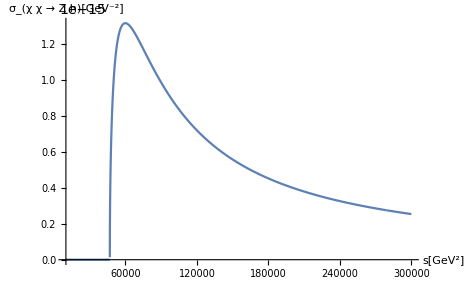

```mathematica
Plot[σxxZh[10^{-3},1,1,s,10],{s,10000,300000},AxesLabel->{"s[GeV^2]","σ_(χ χ  →  Z h)[GeV^-2]"},LabelStyle->Directive[Black,12],PlotPoints-> 10000]
```

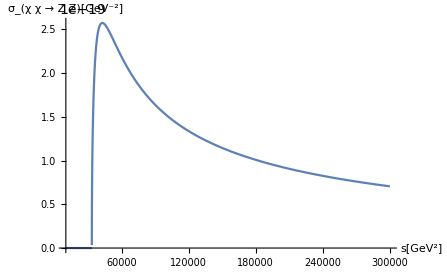

```mathematica
Plot[σxxZZ[10^{-3},1,1,s,10],{s,10000,300000},AxesLabel->{"s[GeV^2]","σ_(χ χ  →  Z Z)[GeV^-2]"},LabelStyle->Directive[Black,12],PlotPoints->10000]
```

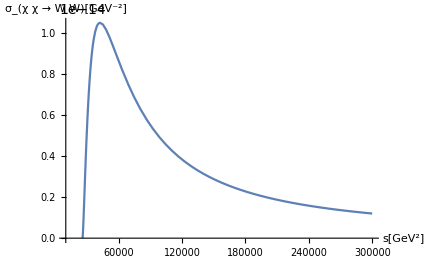

```mathematica
Plot[σxxWW[10^{-3},1,1,s,10],{s,10000,300000},AxesLabel->{"s[GeV^2]","σ_(χ χ  →  W W)[GeV^-2]"},LabelStyle->Directive[Black,12]]
```

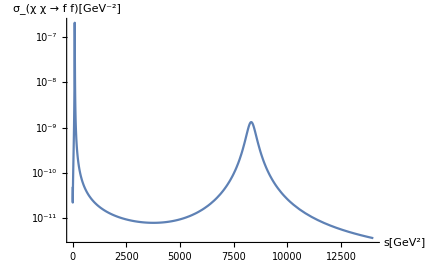

```mathematica
LogPlot[σxxff[10^{-3},1,1,s,10],{s,0,14000},AxesLabel->{"s[GeV^2]","σ_(χ χ  →  f f)[GeV^-2]"},LabelStyle->Directive[Black,12], PlotRange->All]
```

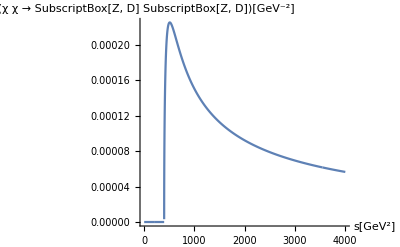

```mathematica
Plot[σxxZdZd[10^{-3},1,1,s,10],{s,0,4000},AxesLabel->{"s[GeV^2]","σ_(χ χ  →  SubscriptBox[Z, D] SubscriptBox[Z, D])[GeV^-2]"},LabelStyle->Directive[Black,12], PlotRange->All,PlotPoints->10000]
```

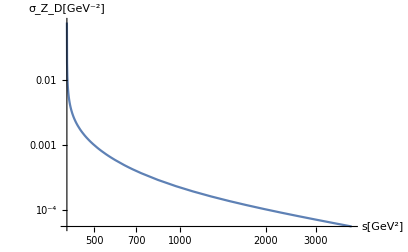

```mathematica
LogLogPlot[σZdZdXX[10^{-3},1,1,s,10],{s,0,4000},AxesLabel->{"s[GeV^2]","σ_Z_D[GeV^-2]"},LabelStyle->Directive[Black,12], PlotRange->All]
```

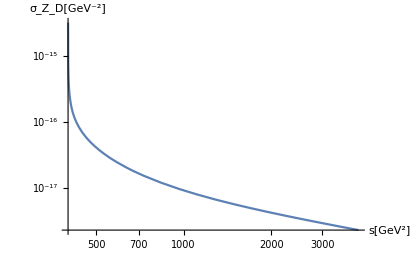

```mathematica
LogLogPlot[σZdZdff[10^{-3},1,1,s,10],{s,0,4000},AxesLabel->{"s[GeV^2]","σ_Z_D[GeV^-2]"},LabelStyle->Directive[Black,12], PlotRange->All]
```

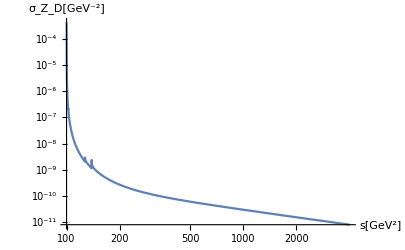

```mathematica
LogLogPlot[σZdfAftot[10^{-3},1,1,s,10],{s,0,4000},AxesLabel->{"s[GeV^2]","σ_Z_D[GeV^-2]"},LabelStyle->Directive[Black,12], PlotRange->All]
```

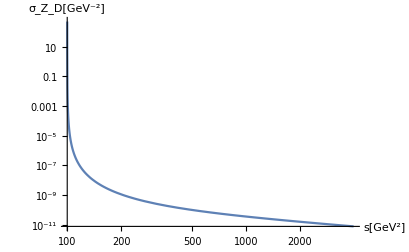

```mathematica
LogLogPlot[σZdAff[10^{-3},1,1,s,10],{s,0,4000},AxesLabel->{"s[GeV^2]","σ_Z_D[GeV^-2]"},LabelStyle->Directive[Black,12], PlotRange->All]
```